# Background code

Hamiltonian used in (High-Power Collective Charging of a Solid-State Quantum Battery): H=ω_c(â)^†â+ω_a J_z+2 ω_c λJ_x((â)^†+â)
where J_z=∑_(i=1)^N σ_z^i and J_x=∑_(i=1)^N σ_x^i
However, i am using ω_A/2∑_(i=1)^N (UnderBar[1]^i-(|g⟩)_i⟨g|+(|e⟩)_i⟨e|)=ω_A/2∑_(i=1)^N (UnderBar[1]^i-σ_z^i) instead of just ω_a J_z 
(This is so g.s corresponds to 0 energy and also if i didnt do this then the excited state would be a higher energy than the g.s which wouldnt work so maybe the different papers have defined Jz differently)
I am also using the RWA: (σ_++σ_-)((â)^†+â)≃σ_+â+σ_-(â)^†  Where is this from, explain??

So in the following notebook i will use this hamiltonian,H=ω_c(â)^†â+ω_A/2∑_(i=1)^N (UnderBar[1]^i-σ_z^i)+2 ω_c λ(σ_+â+σ_-(â)^†) missing i index and sum term

ωa:atomic freq
ωc:cavity freq so at resonance(set ωc=ωa=1 so resonance)
λ:light-atom interaction
γo:optical
γd:dephasing
γt:trap

```mathematica
adagn[n_]:=(matdab[a_,b_]:=Sqrt[b]*KroneckerDelta[a,b+1];
Table[matdab[i,j],{i,1,n+1},{j,1,n+1}])
```

```mathematica
alown[n_]:=(matlab[a_,b_]:=Sqrt[a]*KroneckerDelta[a,b-1];
Table[matlab[i,j],{i,1,n+1},{j,1,n+1}])
```

```mathematica
alown[2]//MatrixForm
```

(0 | 1 | 0
0 | 0 | √2
0 | 0 | 0)

```mathematica
adagn[2]//MatrixForm
```

(0 | 0 | 0
1 | 0 | 0
0 | √2 | 0)

Defining pauli matrices:

```mathematica
sigmaplusR={{0,1},{0,0}};
sigmaminusR=Conjugate[Transpose[sigmaplusR]];
sigmazR=(IdentityMatrix[2]+{{1,0},{0,-1}})/2;(*I've added the identitiy matrix here instead of inserting when im doing the hamiltonian because it makes life easier*)
```

```mathematica
sigmazR
```

{{1,0},{0,0}}

{{1,0},{0,0}} (top left) corresponds to the excitated state. As for the photon matrices adagn and alown, the bottom right corresponds to n-photons and for my inital state i want n-photons and 0 excited atoms, so in this notation it will be the bottom right of the entire density matrix.

```mathematica
FoldKP=Fold[KroneckerProduct];
rho[index_,t_]:=Table[Subscript[ρ, index[[j]],index[[k]]][t],{j,1,Length[index]},{k,1,Length[index]}];
```

```mathematica
L[ρ_,Lo_,γ_]=Simplify[Expand[γ(Conjugate[Transpose[Lo]].Lo.ρ/2+ρ.Conjugate[Transpose[Lo]].Lo/2-Lo.ρ.Conjugate[Transpose[Lo]])]];
dephase[upper_,lower_,size_]:=Module[{matrix},matrix=Table[0,{i,size},{j,size}];matrix[[upper,upper]]=-1;matrix[[lower,lower]]=1;matrix];
L1=dephase[1,2,2];
```

```mathematica
L1ni[n_,j_]:=KroneckerProduct[IdentityMatrix[n+1],FoldKP[Join[Table[ID,j-1],{L1},Table[ID,n-j]]]];(*Above i used the identity matrix again for the photon state as the dissipator will not affect this*)
```

```mathematica
tmax=10.0;
ωa=1;(*atomic freq*)
ωc=1;(*cavity freq so at resonance*)
```

```mathematica
Energystored[n_,λ_,γo_,γd_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];

Plot[Tr[rhonL[t].Hn2nd]/.soln,{t,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"N = "<>ToString[n]},AxesLabel->{"t",""}])
```

The below code is only useful for comparison of 1 atoms to 4 atoms as it just times the energy at the end by 4.

```mathematica
Energystored4[n_,λ_,γo_,γd_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];

Plot[4*Tr[rhonL[t].Hn2nd]/.soln,{t,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"N = "<>ToString[n]}])
```

Power= EMax/tc (Max energy/time it takes to reach max energy)
As this is all we are concerned with for charging.

```mathematica
ChargingPower[n_,λ_,γo_,γd_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];
Plot[Tr[rhonL[t].Hn2nd]/t/.soln,{t,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}])
```

The below code is only useful for comparison of 2 atoms to 4 atoms as it just times the energy at the end by 2.

```mathematica
ChargingRate[n_,λ_,γo_,γd_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax}];
Plot[Tr[rhonL'[t].Hn2nd]/.soln,{t,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"N = "<>ToString[n]},AxesLabel->{"t","Rate"}])
```

```mathematica
ChargingRate4[n_,λ_,γo_,γd_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax}];
Plot[4*Tr[rhonL'[t].Hn2nd]/.soln,{t,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"N = "<>ToString[n]},AxesLabel->{"t","Rate"}])
```

Improved charging rate:

```mathematica
ChargingPower2[n_,λ_,γo_,γd_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];
Plot[2*Tr[rhonL[t].Hn2nd]/t/.soln,{t,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}])
```

```mathematica
poprate[n_,λ_,γo_,γd_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax}];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];
Plot[(Tr[rhonL'[t].firstpop])/.soln,{t,0,tmax/2},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"γo = "<>ToString[γo]},AxesLabel->{"t","Rate"}])
```

```mathematica
tmax=0.07;
poprate[4,1,100,0]
```

$Aborted

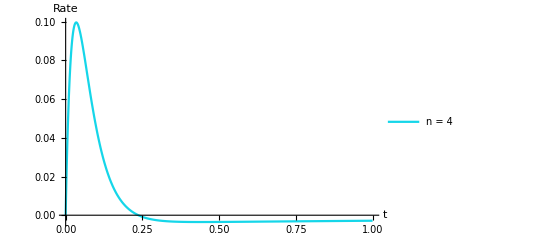

```mathematica
tmax=2;
poprate[4,1,10,0]
```

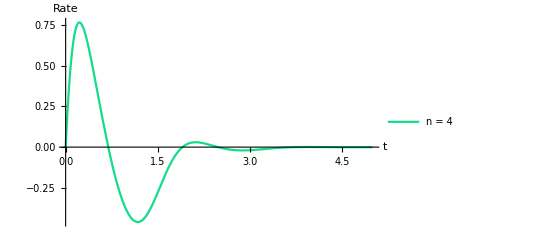

```mathematica
tmax=10;
poprate[4,1,1,0]
```

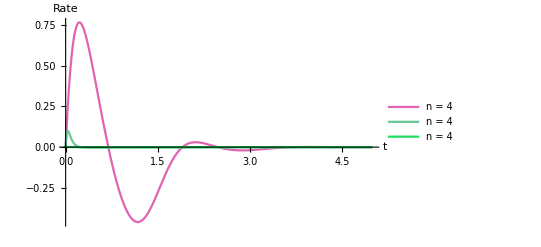

```mathematica
Tmax=4;
Show[poprate[4,1,1,0],poprate[4,1,10,0],poprate[4,1,100,0]]
```

# Modeling hamiltonian

## Energy Stored in excited states:

We solve using Von-Neumann equation with a density operator.
Why?
Our initially pure state will interact with the environment through photons/ phonons that we have no control off. This means correlations between our qubit and the environment will form i.e become entangled. Our environment could be in multiple possible states which means our qubit will be in a “mixed state” which is why we use the density matrix notation. As we go from a pure state to a mixed state we lose our definite phase information in a process called “decoherence”. A mixed state has multiple possible eigenvalues (as the interactions with the environment will cause fluctuations in the energy).

Lets just say λ=1

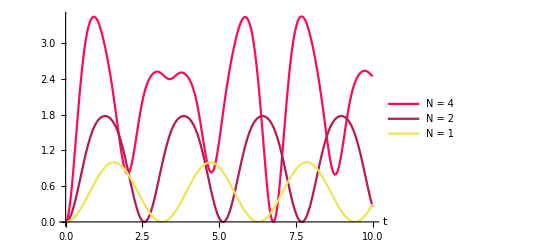

```mathematica
Show[Energystored[4,1,0,0],Energystored[2,1,0,0],Energystored[1,1,0,0]]
```

```mathematica
Show[Energystored[4,1,0,0],Energystored4[1,1,0,0]]
```

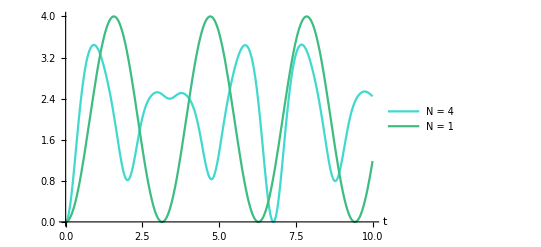

-Graphics-

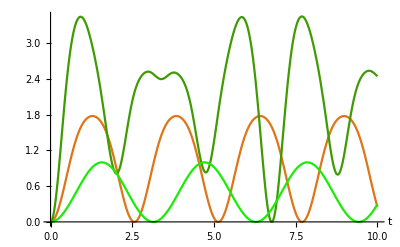

## Power:

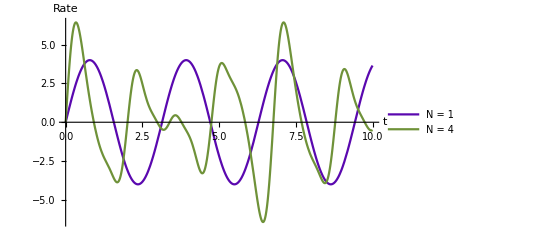

```mathematica
Show[ChargingRate4[1,1,0,0],ChargingRate[4,1,0,0]]
```

Peak values are the only thing we are concerned with in the above, rest is irrelevant as we only care about when it reaches max energy. We see here that for n=4 atoms the charging power is greater than for n=2 atoms.

# Adding Dephasing

Adding a lindblad dissipator for dephasing. This will allow us to access the dark states and prevent superradiant emission so we can actually “store” energy. (improve explanation).

We add the lindblad dissipator term to our Von-Neumann equation which will cause our dephasing,  iℏ(∂ρ)/(∂t)=[H,ρ]-iL(ρ)   
Where L is,
 L(ρ(t))=∑_(i=1)^N γ_i(1/2{L_i^†L_i,ρ(t)}-L_i ρ(t)L_i^†)  
So the Li’s act on each atom, firstly assume γ is the same for all.

Here we use the dephasing operator, L1 = (-1 | 0
0 | 1) which preserves population numbers but will cause the energy levels to fluctuate ??? (From conversation with brendon, cant remember exactly what he said). OR L1 is similiar to Sigma Z matrix which acts as a “phase flip” operator and this will cause coherence to decay and we can see this on the bloch sphere as our state moving inwards in the x-y plane (z stays the same). (Information from Lecture 4 brendon sent and “Thermodynamics of a qubit undergoing dephasing”-(http://iopscience.iop.org/1742-6596/841/1/012019))???

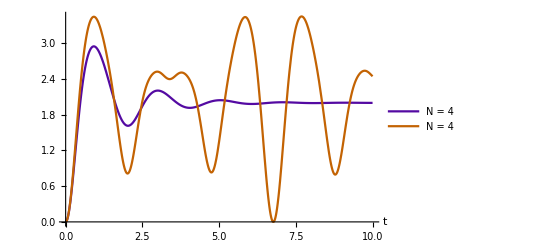

```mathematica
Show[Energystored[4,1,0,0.5],Energystored[4,1,0,0]]
```

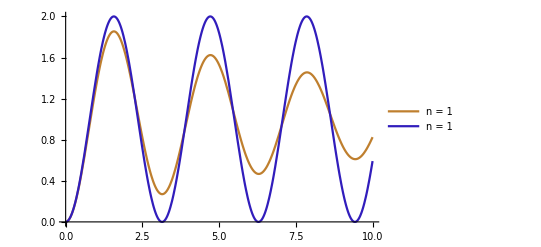

```mathematica
Show[Energystored2[1,1,0,0.1],Energystored2[1,1,0,0]]
```

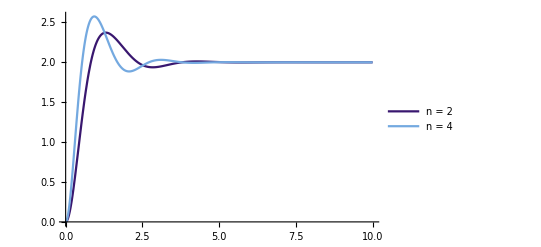

```mathematica
Show[Energystored2[2,1,0,1],Energystored[4,1,0,1]]
```

Reaches half-filled which is expected as “With only dephasing you expect all the atoms to become “half excited” in the long time limit”. Why????

So we see both end up reaching the same plateu in the long time limit but we do see an enhanced charging for n=4 atoms initially:

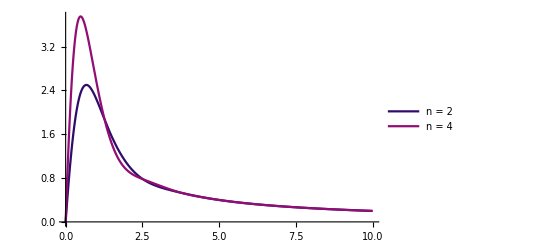

```mathematica
Show[ChargingPower2[2,1,0,1],ChargingPower[4,1,0,1]]
```

# Optical decay

We need to consider spontaneous emission. Here i will use another lindblad dissipator but our operator will be J_-=∑_(i=1)^N σ_-^ias this corresponds to an atom going from excited to ground state (de-exciting). I use this in a Sum because this occurs collectively ???? This will be a superradiant burst !
So remember we have,  L(ρ(t))=∑_(i=1)^N γ_i(1/2{L_i^†L_i,ρ(t)}-L_i ρ(t)L_i^†)
But now our Li will be a sum itself so, L =  J_-=∑_(i=1)^N σ_-^i               (he we are adding it collectively but these could be added incoherently so not superadiant but just random emission for each atom - see sci adv paper, “Superabsorption in an organic microcavity: 
Toward a quantum battery”)
 L(ρ(t))=γ_o(1/2{J_-^†J_-,ρ(t)}-J_-ρ(t)J_-^†) where γ_o will be related to the rate of spontaneous emission.

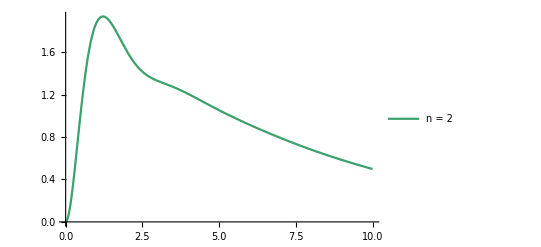

```mathematica
Energystored2[2,1,0.3,1]
```

# Optical decay without dephasing

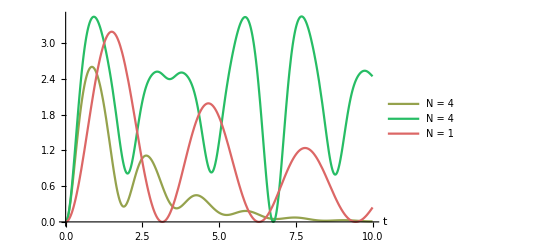

```mathematica
Show[Energystored[4,1,0.3,0],Energystored[4,1,0,0],Energystored4[1,1,0.3,0]]
```

```mathematica
Show[Energystored[4,1,0.3,0],Energystored[4,1,0.3,1]]
```

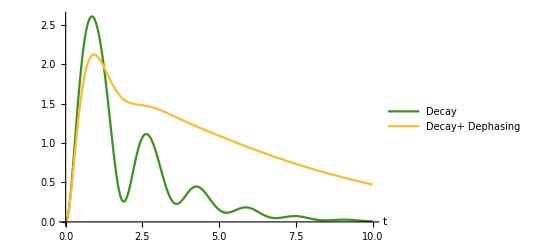

-Graphics-

We can see having our dephasing actually allows us to preserve the excitations better as the “with dephasing” graph remains higher as time goes on so we can store more energy.

# Adding a trap

## Single-atom trap coupled to one atom in system (Trap 1)

I'm going to first look at a single trap atom which is linked to just 1 of my atoms. Here i will model the trap as an external system so i won't involve the properties of the trap in my model (i.e its energy levels etc). I will just be concerned with the rate at which the trap removes excitations from one of the atoms. We can then find the population of the trap (so stored energy) by calculating the population of site 1(for example say atom 1 is the one linked to the trap) * the rate of extraction (γT) then integrating everything over time.

Lindblad operator, L = (σ_-)^1 so only acts on atom at site 1. This will remove exciton from the site 1 atom i.e extracting exciton.

H=ω_c(â)^†â+ω_a ω_A/2∑_(i=1)^N (UnderBar[1]^i-σ_z^i)+2 ω_c λ(σ_+â+σ_-(â)^†)
 iℏ(∂ρ)/(∂t)=[H,ρ]-iL(ρ)  (L=Ld+Lo+Lt)
 Ld(ρ(t))=∑_(i=1)^N γ_d(1/2{L_i^†L_i,ρ(t)}-L_i ρ(t)L_i^†)   (dephasing)
where Li={{-1,0},{0,1}}
 Lo(ρ(t))=γ_o(1/2{J_-^†J_-,ρ(t)}-J_-ρ(t)J_-^†)     (optical decay)
 Lt(ρ(t))=∑_(i=1)^N γ_t(1/2{L_j^†L_j,ρ(t)}-L_j ρ(t)L_j^†)   (trap)
 where Lj = (σ_-)^1

ωa:atomic freq
ωc:cavity freq so at resonance(set ωc=ωa=1 so resonance)
λ:light-atom interaction
γo:optical
γd:dephasing
γt:trap

To find population of trap i first need to find the number of excitons in excited states. I have done this in 2 ways : 
■ Find the excited state population of atom connected to the trap using σ+σ- or {{1,0},{0,0}} (as remember I defined top left as excited state).
■Using J+J- to find number of excitations (can only use this for symmetric cases as this is a collective operator) How this works I’m a little unsure, go over “essay on the theory of collective spontaneous emission” and give a good explanation.

### The code

```mathematica
Trap1Energystored[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom, this takes an excitation from first atom and goes to the "trap"*)
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];

Plot[Tr[rhonL[t].Hn2nd]/.soln,{t,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"N = "<>ToString[n]},AxesLabel->{"t","Energystored"}])
```

Find population of the first site atom which is linked to the trap:

```mathematica
Trap1firstpop[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];
trappop=NIntegrate[γt*Tr[rhonL[t].firstpop]/.soln,{t,0,tmax}];
Show[Plot[Tr[rhonL[t].firstpop]/.soln,{t,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}],
Graphics[Text["Trap population ("<>ToString[n]<>")= "<>ToString[trappop[[1]]],{tmax*0.7,0.000005*n}]]])(*This is just me trying to show both values of trap population on same graph*)
```

```mathematica
Trap1pop[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];
trappop=NIntegrate[γt*Tr[rhonL[t].firstpop]/.soln,{t,0,tmax}])
```

Trap population as a function of time, plotted:

```mathematica
Trap1popPlot[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]},AxesLabel->{"t","Trap population"}])
```

```mathematica
Trap1popPlotm4[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[4*γt*(Tr[rhonL[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]},AxesLabel->{"t","Trap population"}])
```

```mathematica
Trap1popratePlot[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL'[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]},AxesLabel->{"t","Trap charging rate"}])
```

```mathematica
Trap1popratePlotm4[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[4*γt*(Tr[rhonL'[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]},AxesLabel->{"t","Trap charging rate"}])
```

### Optimising

I found optimum values in other Mathematica notebook for n=2 traps:
γd = 42.5315,
 γt = 153.439, 
 trap population = 0.0640081 
 (For n = 2 atoms, λ (g) = 1, γo = 100)

### Comparing 4 atoms to 2 atoms:

Energy stored in energy levels:

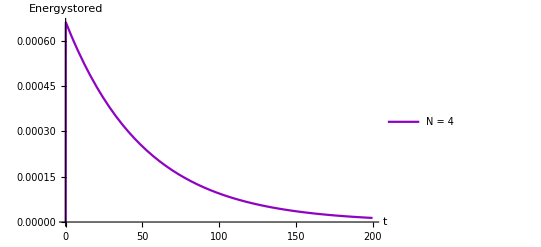

```mathematica
tmax=200;
Trap1Energystored[4,1,100,100,100]
```

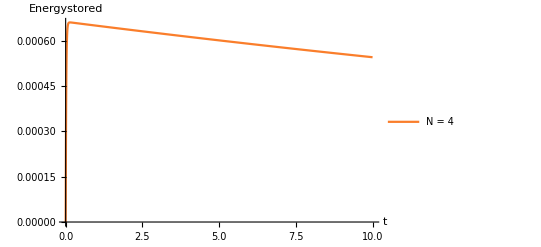

```mathematica
tmax=10;
Trap1Energystored[4,1,100,100,100]
```

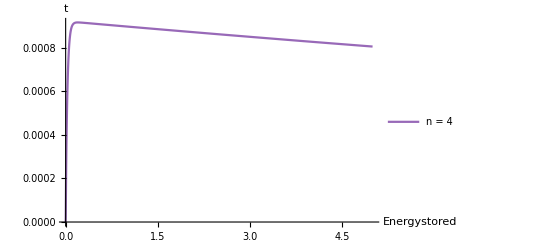

```mathematica
tmax=5;
PLOT1=Trap1Energystored[4,1,100,42.5315,153.439]
```

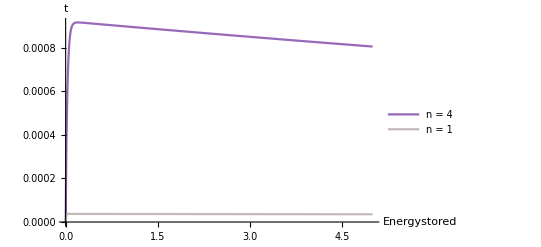

```mathematica
Show[PLOT1,Trap1Energystored[1,1,100,42.5315,153.439]]
```

Looks like an N^2 enhancement, where classically it would be double.

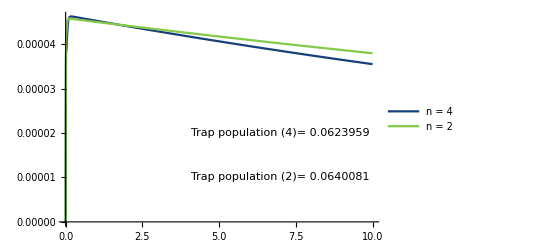

```mathematica
tmax=10;
Show[Trap1firstpop[4,1,100,42.5315,153.439],Trap1firstpop[2,1,100,42.5315,153.439]]
```

However,  we don’t see an enhancement on trap population. We actually see a small reduction.

Energy stored in energy levels at earlier times:

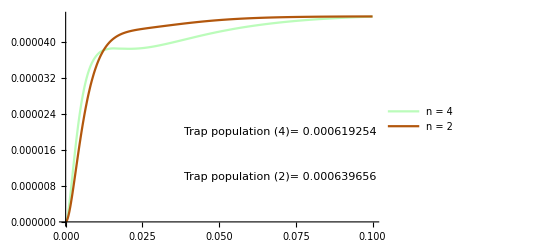

```mathematica
tmax=0.1;
Show[Trap1firstpop[4,1,100,42.5315,153.439],Trap1firstpop[2,1,100,42.5315,153.439]]
```

Trap population as a function of time :

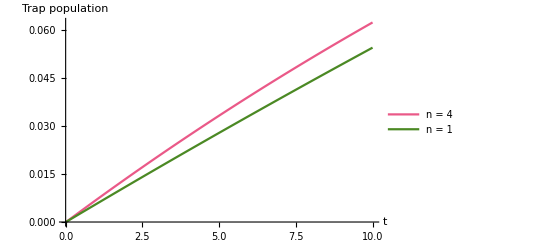

```mathematica
tmax=10;
Show[Trap1popPlot[4,1,100,42.5315,153.439],Trap1popPlot[1,1,100,42.5315,153.439]]
```

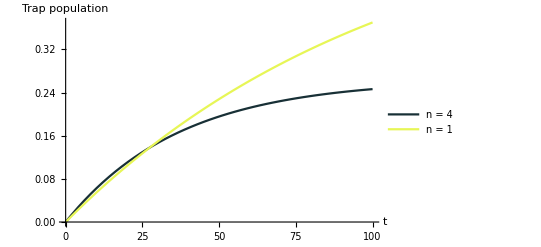

```mathematica
tmax=100;
Show[Trap1popPlot[4,1,100,42.5315,153.439],Trap1popPlot[1,1,100,42.5315,153.439]]
```

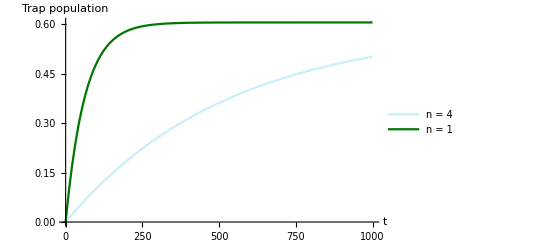

```mathematica
tmax=1000;
Show[Trap1popPlot[4,1,100,2000,153.439],Trap1popPlot[1,1,100,0,153.439]]
```

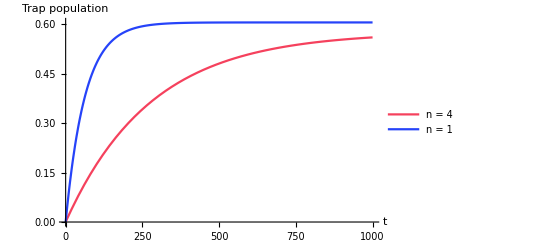

```mathematica
tmax=1000;
Show[Trap1popPlot[4,1,100,1000,153.439],Trap1popPlot[1,1,100,0,153.439]]
```

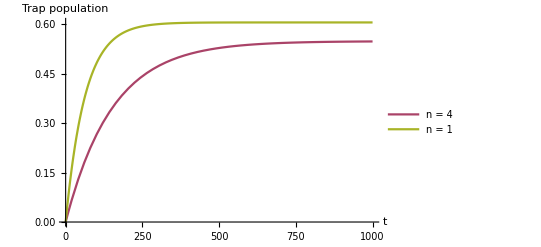

```mathematica
tmax=1000;
Show[Trap1popPlot[4,1,100,500,153.439],Trap1popPlot[1,1,100,0,153.439]]
```

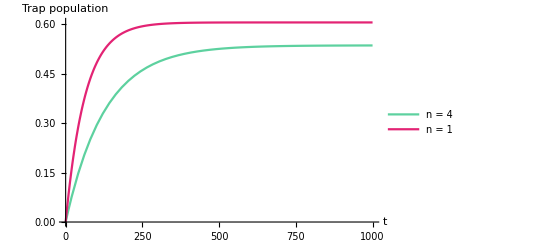

```mathematica
tmax=1000;
Show[Trap1popPlot[4,1,100,400,153.439],Trap1popPlot[1,1,100,0,153.439]]
```

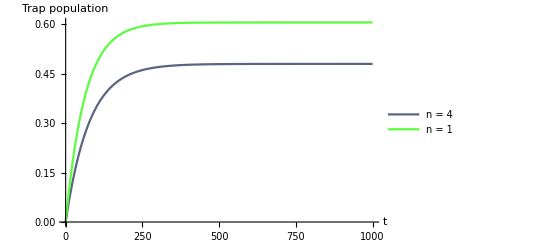

```mathematica
tmax=1000;
Show[Trap1popPlot[4,1,100,200,153.439],Trap1popPlot[1,1,100,0,153.439]]
```

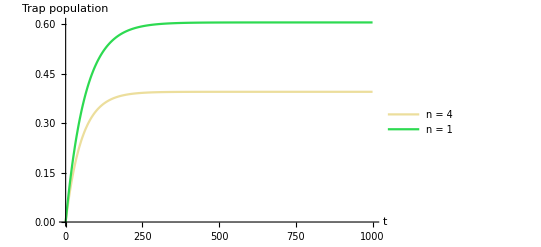

```mathematica
tmax=1000;
Show[Trap1popPlot[4,1,100,100,153.439],Trap1popPlot[1,1,100,0,153.439]]
```

Need to compare to dph=0 in single atom case, as no advantage from dephasing in single-atom case!

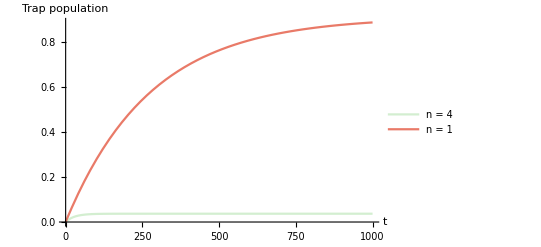

```mathematica
tmax=1000;
Show[Trap1popPlot[4,1,100,10,1000],Trap1popPlot[1,1,100,0,1000]]
```

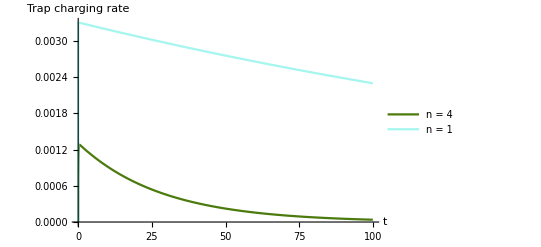

```mathematica
tmax=100;
Show[Trap1popratePlot[4,1,100,10,1000],Trap1popratePlot[1,1,100,0,1000]]
```

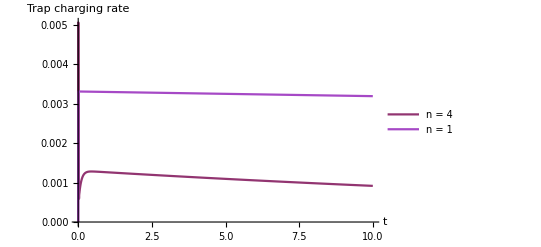

```mathematica
tmax=10;
Show[Trap1popratePlot[4,1,100,10,1000],Trap1popratePlot[1,1,100,0,1000]]
```

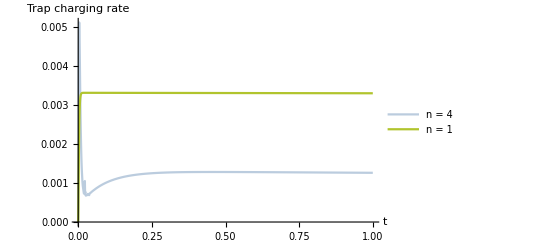

```mathematica
tmax=1;
Show[Trap1popratePlot[4,1,100,10,1000],Trap1popratePlot[1,1,100,0,1000]]
```

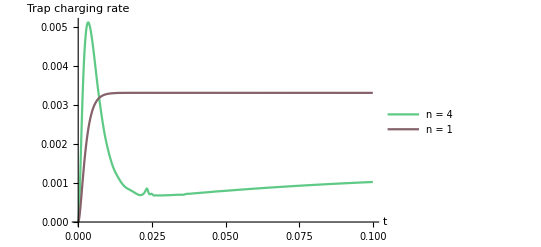

```mathematica
tmax=0.1;
Show[Trap1popratePlot[4,1,100,10,1000],Trap1popratePlot[1,1,100,0,1000]]
```

```mathematica
tmax=1000;Show[Trap1popPlot[4,1,100,1,1000],Trap1popPlot[4,1,100,10,1000],Trap1popPlot[4,1,100,100,1000],Trap1popPlot[4,1,100,1000,1000],Trap1popPlot[1,1,100,0,1000]]
```

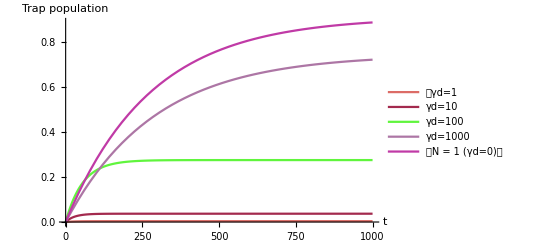

Syntax::sntxf: "LineLegend[{Directive[Opacity[1.],AbsoluteThickness[1.6],]}," cannot be followed by "{"γd=1},LegendMarkers→None,LabelStyle→{},LegendLayout→Column]".

```mathematica
tmax=100;Show[Trap1popratePlot[4,1,100,1,1000],Trap1popratePlot[4,1,100,10,1000],Trap1popratePlot[4,1,100,100,1000],Trap1popratePlot[4,1,100,1000,1000],Trap1popratePlot[1,1,100,0,1000]]
```

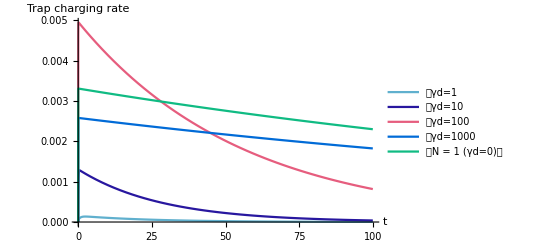

```mathematica
tmax=0.1;Show[Trap1popratePlot[4,1,100,1,1000],Trap1popratePlot[4,1,100,10,1000],Trap1popratePlot[4,1,100,100,1000],Trap1popratePlot[4,1,100,1000,1000],Trap1popratePlot[1,1,100,0,1000]]
```

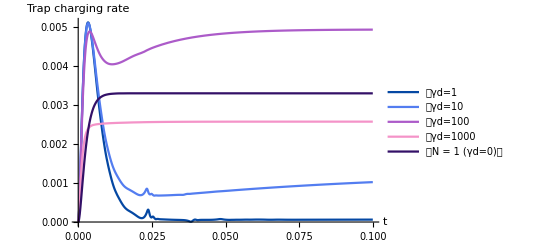

```mathematica
tmax=1000;Show[Trap1popratePlot[4,1,100,1,1000],Trap1popratePlot[4,1,100,10,1000],Trap1popratePlot[4,1,100,100,1000],Trap1popratePlot[4,1,100,1000,1000],Trap1popratePlot[1,1,100,0,1000]]
```

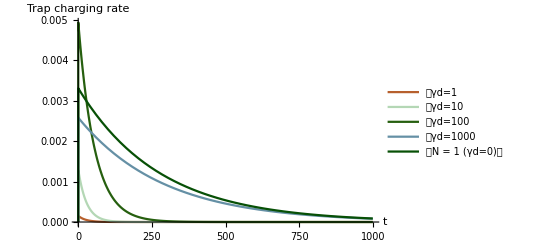

We will take λd=100 and increase trap rate, as this is where we saw a significant enhancement in rate but trap population can still improve.

CHANGING TRAP RATE γ_d=100:

```mathematica
tmax=1000;Show[Trap1popPlot[4,1,100,100,1],
Trap1popPlot[4,1,100,100,10],Trap1popPlot[4,1,100,100,100],Trap1popPlot[4,1,100,100,1000],Trap1popPlot[4,1,100,100,10000]]
```

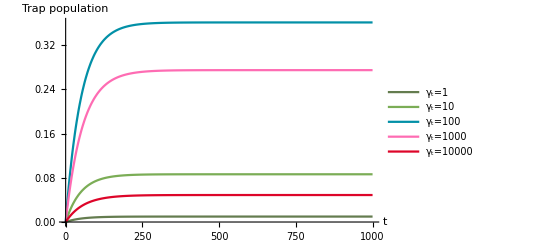

```mathematica
tmax=300;Show[Trap1popratePlot[4,1,100,100,1],
Trap1popratePlot[4,1,100,100,10],Trap1popratePlot[4,1,100,100,100],Trap1popratePlot[4,1,100,100,1000],Trap1popratePlot[4,1,100,100,10000]]
```

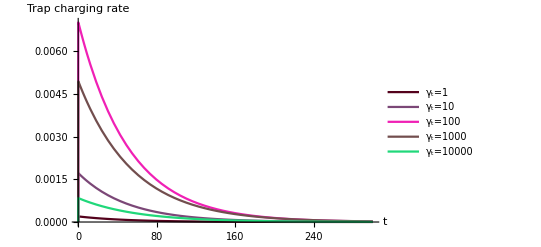

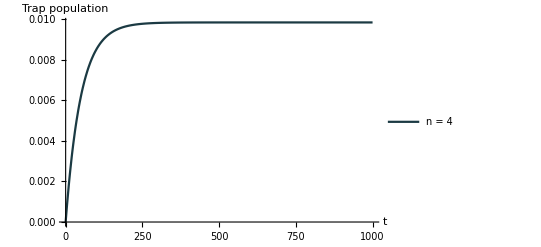

```mathematica
tmax=1000;
Trap1popPlot[4,1,100,100,1]
```

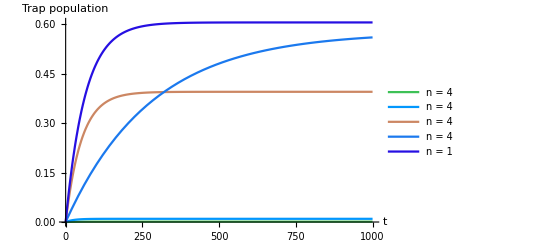

```mathematica
tmax=1000;Show[Trap1popPlot[4,1,100,0.1,153.439],Trap1popPlot[4,1,100,1,153.439],Trap1popPlot[4,1,100,100,153.439],Trap1popPlot[4,1,100,1000,153.439],Trap1popPlot[1,1,100,0,153.439]]
```

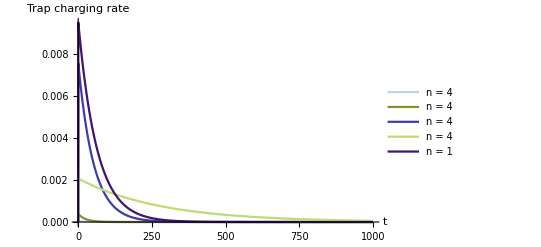

```mathematica
tmax=1000;Show[Trap1popratePlot[4,1,100,0.1,153.439],Trap1popratePlot[4,1,100,1,153.439],Trap1popratePlot[4,1,100,100,153.439],Trap1popratePlot[4,1,100,1000,153.439],Trap1popratePlot[1,1,100,0,153.439]]
```

I SEE SUPERABSORB IN ABOUT 0.01 SECS IN SUPERRAD EXAMPLE AT END,  I NEED TO INCREASE TRAPPING RATE MASSIVELY I RECKON, ITS FINE TO INCLUDE THESE GRAPHS BECAUSE I CAN THEN SAY AFTER WE NEED TO INCREASE TRAPPING

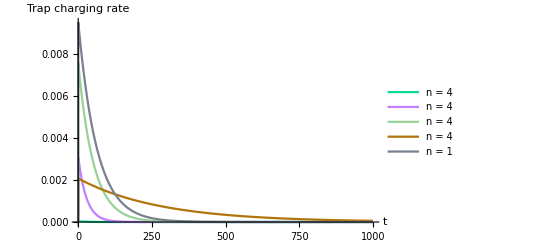

```mathematica
tmax=100;Show[Trap1popratePlot[4,1,100,0.1,153.439],Trap1popratePlot[4,1,100,10,153.439],Trap1popratePlot[4,1,100,100,153.439],Trap1popratePlot[4,1,100,1000,153.439],Trap1popratePlot[1,1,100,0,153.439]]
```

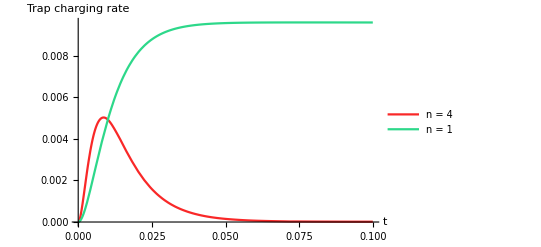

```mathematica
tmax=0.1;
Show[Trap1popratePlot[4,1,100,0.1,150],Trap1popratePlot[1,1,100,0,150]]
```

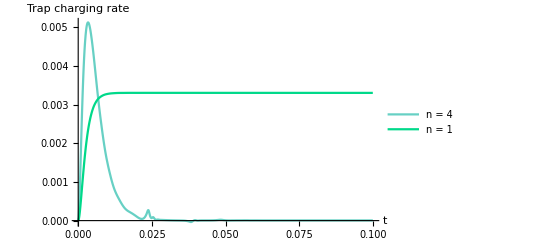

```mathematica
tmax=0.1;
Show[Trap1popratePlot[4,1,100,0.1,1000],Trap1popratePlot[1,1,100,0,1000]]
```

```mathematica
tmax=10000;
Show[Trap1popPlot[4,1,100,1,153.439],Trap1popPlot[4,1,100,1000,153.439],Trap1popPlot[4,1,100,10000,153.439],Trap1popPlot[1,1,100,1,153.439]]
```

$Aborted

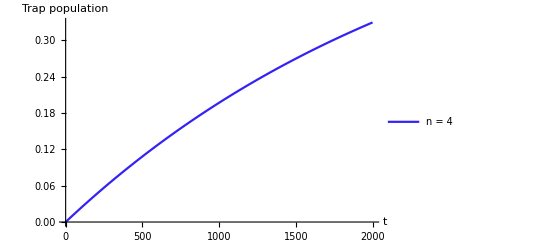

```mathematica
tmax=2000;
Trap1popPlot[4,1,100,10000,153.439]
```

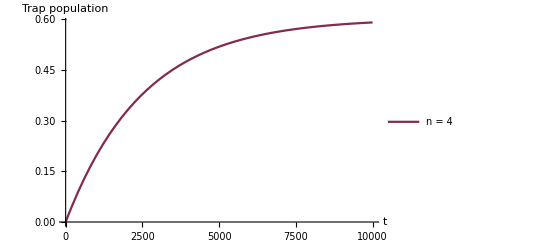

```mathematica
tmax=10000;
Trap1popPlot[4,1,100,10000,153.439]
```

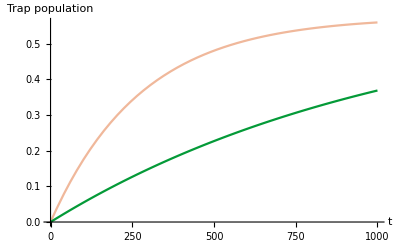

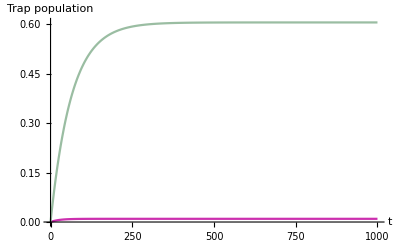

Why is it that when dephasing is weak there is more stored in trap linked to N=1 system?? we see these bad effects when dephasing rate is less that optical decay rate. we need the excitons stored in our dark states before they are superradiantly emitted. The reason for the massive reduction for N=4 system is because the superradiant rate is proportional to N^2!

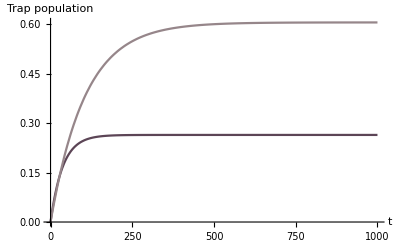

```mathematica
tmax=1/100;
Show[Trap1popPlot[4,1,100,42.5315,153.439],Trap1popPlot[1,1,100,42.5315,153.439]]
```

$Aborted

At large times they both behave very similarly. Maybe because at large times (where the atom-light interactions have died down in the way that remember in previous notebook we would see a peak) the trap extraction takes over and as this is the same for both, we get the same “charging”. 
So we see classical behaviour at large times, why?
So if we look below we see in the long time limit all atoms become “half excited” and this might be why we see similar behaviour n=2 and n=4 with out trap at large times.

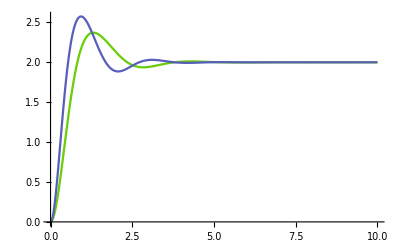

with optical decay:

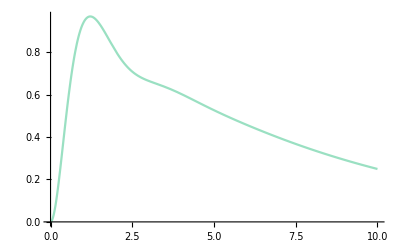

At earlier times:

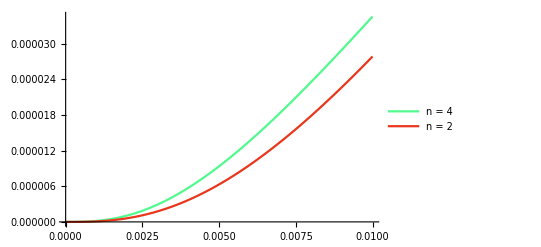

```mathematica
tmax=1/100;
Show[Trap1popPlot[4,1,100,42.5315,153.439],Trap1popPlot[2,1,100,42.5315,153.439]]
```

So at large times, we see classical behaviour. This means all atoms can be treated independently so if we just consider 1 atom from the 2-atom, 2-photons system, it will act identically to 1 atom from the 4-atom, 4-photon system. This is why we see the trap population being the same. As the first atom population (where we get the trap pop from) will be the same.
But for small times, we actually see an increase in trap population for n=4. This is shows an enhanced charging rate. Why only at small times ?(similar to question above, its this superabs burst)

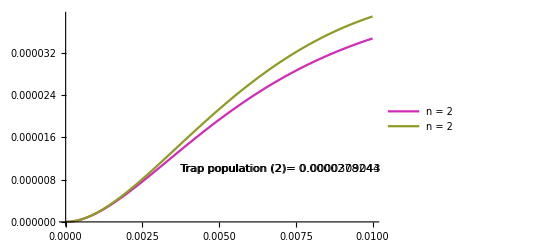

```mathematica
Show[Trap1firstpop[2,1,100,42.5315,153.439],Trap1firstpop[2,1,100,1,153.439]]
```

```mathematica
Trap1pop[2,1,100,42.5315,153.439]
```

{0.0640081}

```mathematica
Trap1pop[2,1,100,20,153.439]
```

```mathematica
list1=Table[{x,y,Trap1pop[2,1,100,x,y][[1]]},{x,10,70,5},{y,120,180,5}]
```

{{{10,120,0.0448771},{10,125,0.0445998},{10,130,0.0443087},{10,135,0.0440062},{10,140,0.0436946},{10,145,0.0433755},{10,150,0.0430508},{10,155,0.0427216},{10,160,0.0423893},{10,165,0.0420547},{10,170,0.0417187},{10,175,0.0413821},{10,180,0.0410456}},{{15,120,0.0535886},{15,125,0.0533939},{15,130,0.0531739},{15,135,0.0529321},{15,140,0.0526718},{15,145,0.0523956},{15,150,0.0521059},{15,155,0.0518049},{15,160,0.0514943},{15,165,0.0511757},{15,170,0.0508505},{15,175,0.0505199},{15,180,0.0501851}},{{20,120,0.058614},{20,125,0.0585168},{20,130,0.0583853},{20,135,0.058224},{20,140,0.0580365},{20,145,0.0578262},{20,150,0.057596},{20,155,0.0573485},{20,160,0.0570859},{20,165,0.0568103},{20,170,0.0565234},{20,175,0.0562269},{20,180,0.0559221}},{{25,120,0.0614403},{25,125,0.0614366},{25,130,0.061392},{25,135,0.0613115},{25,140,0.0611991},{25,145,0.0610586},{25,150,0.0608932},{25,155,0.0607059},{25,160,0.0604991},{25,165,0.0602752},{25,170,0.0600362},{25,175,0.0597839},{25,180,0.05952}},{{30,120,0.0628886},{30,125,0.0629683},{30,130,0.0630027},{30,135,0.0629967},{30,140,0.0629547},{30,145,0.0628806},{30,150,0.0627779},{30,155,0.0626496},{30,160,0.0624984},{30,165,0.062327},{30,170,0.0621374},{30,175,0.0619317},{30,180,0.0617116}},{{35,120,0.0634447},{35,125,0.0635968},{35,130,0.0637004},{35,135,0.0637606},{35,140,0.0637817},{35,145,0.0637679},{35,150,0.0637226},{35,155,0.0636491},{35,160,0.0635503},{35,165,0.0634287},{35,170,0.0632865},{35,175,0.063126},{35,180,0.062949}},{{40,120,0.0634109},{40,125,0.0636248},{40,130,0.0637881},{40,135,0.0639058},{40,140,0.0639825},{40,145,0.0640222},{40,150,0.0640284},{40,155,0.0640045},{40,160,0.0639533},{40,165,0.0638774},{40,170,0.0637793},{40,175,0.0636611},{40,180,0.0635247}},{{45,120,0.0629823},{45,125,0.0632485},{45,130,0.0634628},{45,135,0.0636302},{45,140,0.0637552},{45,145,0.0638418},{45,150,0.0638935},{45,155,0.0639137},{45,160,0.0639053},{45,165,0.0638708},{45,170,0.0638128},{45,175,0.0637333},{45,180,0.0636343}},{{50,120,0.0622888},{50,125,0.0625991},{50,130,0.0628567},{50,135,0.0630667},{50,140,0.0632334},{50,145,0.0633608},{50,150,0.0634525},{50,155,0.0635117},{50,160,0.0635412},{50,165,0.0635438},{50,170,0.0635218},{50,175,0.0634773},{50,180,0.0634125}},{{55,120,0.0614187},{55,125,0.0617659},{55,130,0.0620604},{55,135,0.0623067},{55,140,0.0625094},{55,145,0.0626722},{55,150,0.0627987},{55,155,0.062892},{55,160,0.0629552},{55,165,0.0629906},{55,170,0.0630008},{55,175,0.0629879},{55,180,0.0629539}},{{60,120,0.0604331},{60,125,0.0608113},{60,130,0.0611368},{60,135,0.0614141},{60,140,0.0616476},{60,145,0.061841},{60,150,0.0619978},{60,155,0.0621212},{60,160,0.0622139},{60,165,0.0622785},{60,170,0.0623174},{60,175,0.0623326},{60,180,0.0623263}},{{65,120,0.0593749},{65,125,0.0597789},{65,130,0.0601306},{65,135,0.0604343},{65,140,0.0606942},{65,145,0.060914},{65,150,0.0610972},{65,155,0.0612467},{65,160,0.0613654},{65,165,0.0614557},{65,170,0.0615201},{65,175,0.0615605},{65,180,0.061579}},{{70,120,0.0582744},{70,125,0.0587},{70,130,0.0590736},{70,135,0.0593996},{70,140,0.0596822},{70,145,0.0599248},{70,150,0.0601308},{70,155,0.0603032},{70,160,0.0604447},{70,165,0.0605577},{70,170,0.0606447},{70,175,0.0607075},{70,180,0.0607481}}}

```mathematica
ListPlot3D[Join[list1[[1]],list1[[2]],list1[[3]],list1[[4]],list1[[5]],list1[[6]],list1[[7]],list1[[8]],list1[[9]],list1[[10]],list1[[11]],list1[[12]],list1[[13]]]]
```

-Graphics3D-

## 2 Atom traps coupled to 2 different atoms (Trap 2)

### The code

```mathematica
Trap2Energystored[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom*)
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
(*acts only on second atom - This is our "second trap"*)(*so we are just removing excitions again but from 2 atoms now*)
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]-ⅈ*L[rhonL[t],sigminus2,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];

Plot[Tr[rhonL[t].Hn2nd]/.soln,{t,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}])
```

But now we need to consider 2nd atom population as well as first. This is because we have trap linked to both, so overall trap population will be the sum of both.

```mathematica
Trap2firstsecpop[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]-ⅈ*L[rhonL[t],sigminus1,γt]-ⅈ*L[rhonL[t],sigminus2,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];
trappop=NIntegrate[γt*(Tr[rhonL[t].firstpop]+Tr[rhonL[t].secpop])/.soln,{t,0,tmax}];
Show[Plot[(Tr[rhonL[t].firstpop]+Tr[rhonL[t].secpop])/.soln,{t,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}],
Graphics[Text["Trap population ("<>ToString[n]<>")= "<>ToString[trappop[[1]]],{tmax*0.7,0.000005*n}]]])(*This is just me trying to show both values of trap population on same graph*)
```

Now just trap population:

```mathematica
Trap2pop[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]-ⅈ*L[rhonL[t],sigminus1,γt]-ⅈ*L[rhonL[t],sigminus2,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];
trappop=NIntegrate[γt*(Tr[rhonL[t].firstpop]+Tr[rhonL[t].secpop])/.soln,{t,0,tmax}])
```

```mathematica
Trap2popPlot[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]-ⅈ*L[rhonL[t],sigminus1,γt]-ⅈ*L[rhonL[t],sigminus2,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];
Plot[NIntegrate[γt*(Tr[rhonL[t].firstpop]+Tr[rhonL[t].secpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}])
```

### Comparing 4 atoms to 2 atoms:

Energy stored in energy levels :

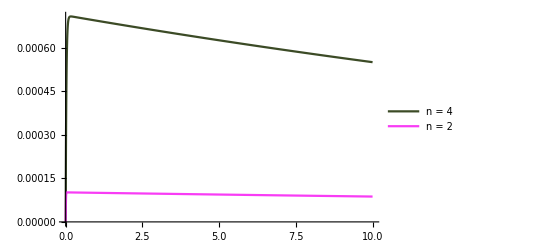

```mathematica
tmax=10;
Show[Trap2Energystored[4,1,100,42.5315,153.439],Trap2Energystored[2,1,100,42.5315,153.439]]
```

Much more than double, therefore enhanced energy stored in energy levels.

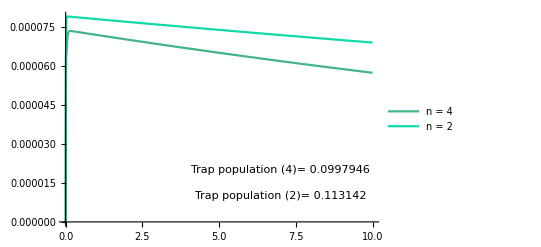

```mathematica
tmax=10;
Show[Trap2firstsecpop[4,1,100,42.5315,153.439],Trap2firstsecpop[2,1,100,42.5315,153.439]]
```

Trap population is less, how, why ??? Surely it would be the same if what i discussed earlier about behaving classically at large times was true. Because this would mean the graphs should be the same at large times. (As atoms act same as isolated atoms, so two traps on two atoms would be the same for both systems)
Maybe because i’ve optimised for n=2 atoms, if i optimise for both then maybe i’ll get the same (or similar)

Trap population as a function of time :

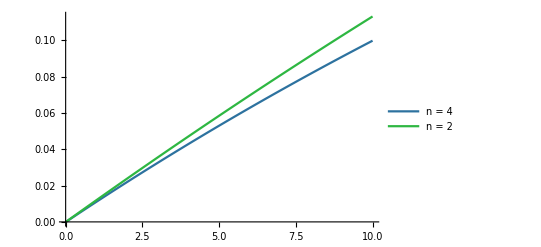

```mathematica
tmax=10;
Show[Trap2popPlot[4,1,100,42.5315,153.439],Trap2popPlot[2,1,100,42.5315,153.439]]
```

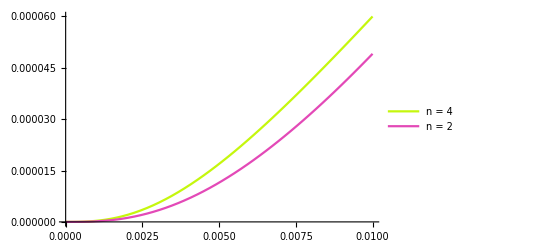

```mathematica
tmax=1/100;
Show[Trap2popPlot[4,1,100,42.5315,153.439],Trap2popPlot[2,1,100,42.5315,153.439]]
```

So again, at earlier times, we see this enhanced charging for n=4 atoms. But why at later times is n=2 larger than n=4?  (is it because i haven’t optimised, is it because 2 traps for 2 atoms allows us to take advantage of collective behaviour better than 2 traps for 4 atoms?)

## Trap linked to all n-atoms (so n-traps) (Trap 3)

### The code

```mathematica
Trap3Energystored[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom*)
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
(*acts only on second atom - This is our "second trap"*)(*so we are just removing excitions again but from 2 atoms now*)
sigminusi[i_]:=KroneckerProduct[IdentityMatrix[n+1],FoldKP[Table[ID,i]],FoldKP[sigmaminusR,Table[ID,n-i-1]]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
L3=Sum[L[rhonL[t],sigminusi[x],γt],{x,1,n-1}]+L[rhonL[t],sigminus1,γt];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L3];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];
Plot[Tr[rhonL[t].Hn2nd]/.soln,{t,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}])
```

Plot to show the population of one of the atoms:

```mathematica
Trap3Allpop[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom*)
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
(*acts only on second atom - This is our "second trap"*)(*so we are just removing excitions again but from 2 atoms now*)
sigminusi[i_]:=KroneckerProduct[IdentityMatrix[n+1],FoldKP[Table[ID,i]],FoldKP[sigmaminusR,Table[ID,n-i-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
L3=Sum[L[rhonL[t],sigminusi[x],γt],{x,1,n-1}]+L[rhonL[t],sigminus1,γt];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L3];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];
trappop=NIntegrate[n*γt*(Tr[rhonL[t].firstpop])/.soln,{t,0,tmax}];
Show[Plot[(Tr[rhonL[t].firstpop])/.soln,{t,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}],
Graphics[Text["Trap population ("<>ToString[n]<>")= "<>ToString[trappop[[1]]],{tmax*0.7,0.000005*n}]]])(*This is just me trying to show both values of trap population on same graph*)
```

Gives trap population value:

```mathematica
Trap3pop[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom*)
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
(*acts only on second atom - This is our "second trap"*)(*so we are just removing excitions again but from 2 atoms now*)
sigminusi[i_]:=KroneckerProduct[IdentityMatrix[n+1],FoldKP[Table[ID,i]],FoldKP[sigmaminusR,Table[ID,n-i-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
L3=Sum[L[rhonL[t],sigminusi[x],γt],{x,1,n-1}]+L[rhonL[t],sigminus1,γt];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L3];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];
trappop=NIntegrate[n*γt*(Tr[rhonL[t].firstpop])/.soln,{t,0,tmax}])
```

Plots trap population as a function of time:

```mathematica
Trap3popPlot[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom*)
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
(*acts only on second atom - This is our "second trap"*)(*so we are just removing excitions again but from 2 atoms now*)
sigminusi[i_]:=KroneckerProduct[IdentityMatrix[n+1],FoldKP[Table[ID,i]],FoldKP[sigmaminusR,Table[ID,n-i-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
L3=Sum[L[rhonL[t],sigminusi[x],γt],{x,1,n-1}]+L[rhonL[t],sigminus1,γt];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L3];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[n*γt*(Tr[rhonL[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}])
```

```mathematica
Trap3popratePlot[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom*)
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
(*acts only on second atom - This is our "second trap"*)(*so we are just removing excitions again but from 2 atoms now*)
sigminusi[i_]:=KroneckerProduct[IdentityMatrix[n+1],FoldKP[Table[ID,i]],FoldKP[sigmaminusR,Table[ID,n-i-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
L3=Sum[L[rhonL[t],sigminusi[x],γt],{x,1,n-1}]+L[rhonL[t],sigminus1,γt];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L3];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[n*γt*(Tr[rhonL'[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]},AxesLabel->{"t","Trap charging rate"}])
```

multiplied by 4:

```mathematica
Trap3popPlotm4[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom*)
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
(*acts only on second atom - This is our "second trap"*)(*so we are just removing excitions again but from 2 atoms now*)
sigminusi[i_]:=KroneckerProduct[IdentityMatrix[n+1],FoldKP[Table[ID,i]],FoldKP[sigmaminusR,Table[ID,n-i-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
L3=Sum[L[rhonL[t],sigminusi[x],γt],{x,1,n-1}]+L[rhonL[t],sigminus1,γt];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L3];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[4*n*γt*(Tr[rhonL[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}])
```

```mathematica
Trap3popratePlotm4[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom*)
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
(*acts only on second atom - This is our "second trap"*)(*so we are just removing excitions again but from 2 atoms now*)
sigminusi[i_]:=KroneckerProduct[IdentityMatrix[n+1],FoldKP[Table[ID,i]],FoldKP[sigmaminusR,Table[ID,n-i-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
L3=Sum[L[rhonL[t],sigminusi[x],γt],{x,1,n-1}]+L[rhonL[t],sigminus1,γt];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L3];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[4*n*γt*(Tr[rhonL'[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}])
```

Using J+J- to find number of excitations instead of .firstpop :
(essay on the theory of collective spontaneous emission used this for ... ?)

Can i do this for n traps linked to n atoms? so this is a collective operator, so to use this we need everything to be symmetrical and identical which will be the case here (unlike for 1 and 2 traps). So i think i can use it here. I can definitely use it for trap 4 (one trap collectively linked to all atoms).

```mathematica
Trap3popPlot2[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom*)
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
(*acts only on second atom - This is our "second trap"*)(*so we are just removing excitions again but from 2 atoms now*)
sigminusi[i_]:=KroneckerProduct[IdentityMatrix[n+1],FoldKP[Table[ID,i]],FoldKP[sigmaminusR,Table[ID,n-i-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
L3=Sum[L[rhonL[t],sigminusi[x],γt],{x,1,n-1}]+L[rhonL[t],sigminus1,γt];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L3];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];
Plot[NIntegrate[γt*(Tr[rhonL[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}])
```

### Comparing 4 atoms to 2 atoms (using σ+σ- to measure excitations):

```mathematica
tmax=1000;
Show[Trap3popPlot[4,1,100,100,100],Trap3popPlotm4[1,1,100,100,100],Trap1popPlotm4[4,1,100,100,100],Trap1popPlotm4[1,1,100,100,100]]
```

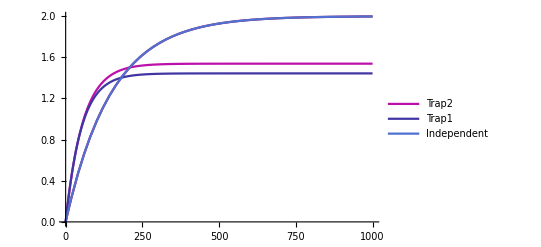

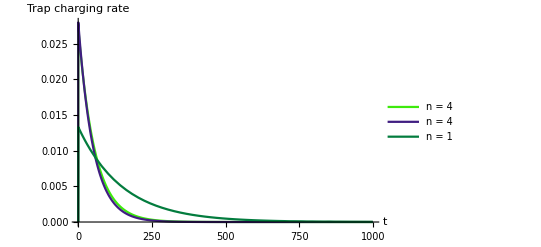

```mathematica
tmax=1000;
Show[Trap3popratePlot[4,1,100,100,100],Trap1popratePlotm4[4,1,100,100,100],Trap1popratePlotm4[1,1,100,100,100]]
```

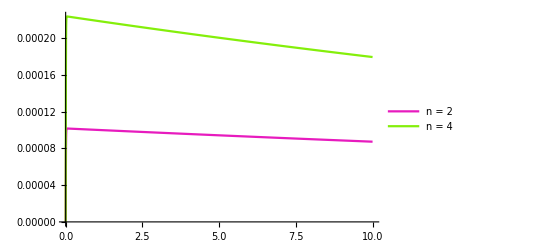

```mathematica
tmax=10;Show[Trap3Energystored[2,1,100,42.5315,153.439],Trap3Energystored[4,1,100,42.5315,153.439]]
```

We can see this is roughly double, which is expected for isolated atoms. So lets look at earlier times :

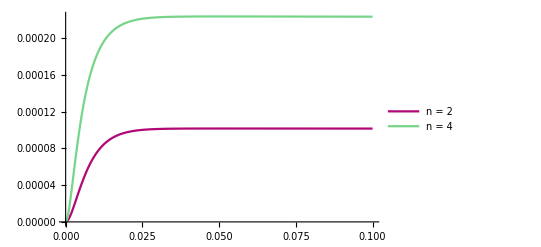

```mathematica
tmax=0.1;Show[Trap3Energystored[2,1,100,42.5315,153.439],Trap3Energystored[4,1,100,42.5315,153.439]]
```

Just over double so seems enhanced. But remember there are 4 traps linked to n=4 case which are all extracting energy so compared to n=2 atoms which only had 2 traps, we should see a increased reduction in energy stored in energy levels for 4 atoms. So this looks okay.

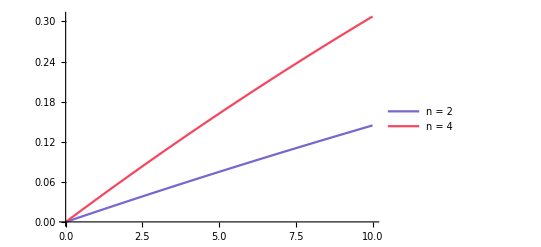

```mathematica
tmax=10;
Show[Trap3popPlot[2,1,100,42.5315,153.439],Trap3popPlot[4,1,100,42.5315,153.439]]
```

at large times, the behaviour is linear (why????) so i need to reduce the time to see its initial charging rate. However, we do see the trap population increasing by about two times more (judging by gradient) but that is just because we have double the amount of traps thus extracting double the amount.

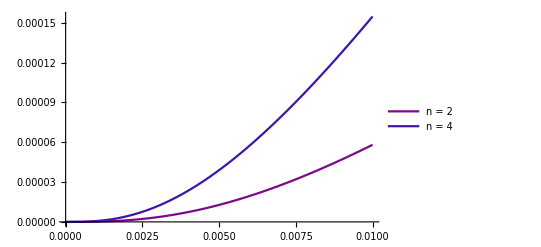

```mathematica
tmax=1/100;
Show[Trap3popPlot[2,1,100,42.5315,153.439],Trap3popPlot[4,1,100,42.5315,153.439]]
```

So here we see trap population does increase much faster for n=4 atoms than n=2 atoms. So this is superextensive charging right? Not sure, as we do have double the amount of traps connected but gradient does seem to me more than double here. There are ways i could see if the it is more than double (could try find gradients, could just multiply by 2 and compare etc ... ) which i should do.

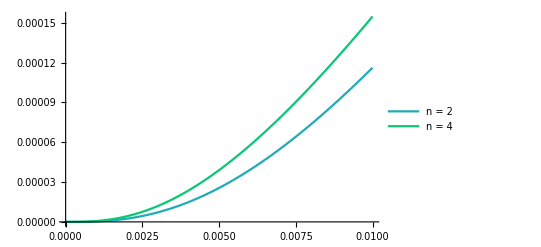

```mathematica
tmax=1/100;
Show[Trap3popPlotm2[2,1,100,42.5315,153.439],Trap3popPlot[4,1,100,42.5315,153.439]]
```

### Comparing 4 atoms to 2 atoms (using J+J- to measure excitations):

Energy stored is same as other method. All this changes is calculating trap population.

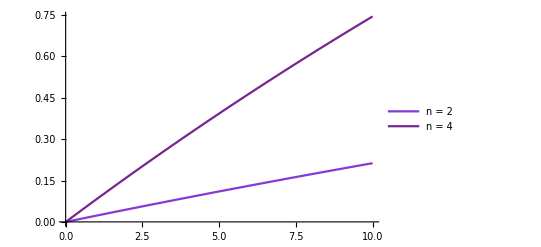

```mathematica
tmax=10;Show[Trap3popPlot2[2,1,100,42.5315,153.439],Trap3popPlot2[4,1,100,42.5315,153.439]]
```

Here we see a more than double rate of charging even at larger times. This means we find an enhancement at all times!

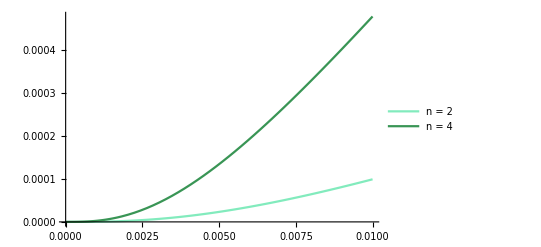

```mathematica
tmax=1/100;Show[Trap3popPlot2[2,1,100,42.5315,153.439],Trap3popPlot2[4,1,100,42.5315,153.439]]
```

Comparing to σ+σ- to measure excitations (Below). We see that trap populations have increased a lot more in this given time and we can see a much greater advantage of using n=4 atoms than n=2 atoms. This suggests using the single atom operators (σ+σ- ) doesn’t give us all the possible excitons so we cant fully appreciate the quantum advantage. Why ???? with σ+σ- i find the trap population by first asking for how many excitons in the excited state of of first atom then multiplying by n (or 2 etc depending on number of trap2) to find trap population (i also multiply by γt). This however, does not include coherences. Can coherence’s decay to give off excitons to? does J+J- therefore allow us to measure these excitons hidden in the coherences?

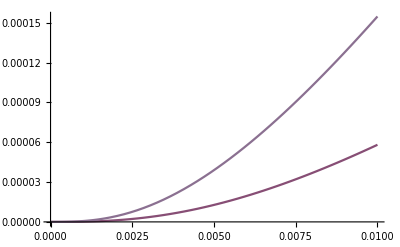

## 1 trap atom coupled collectively to all atoms. (Trap 4)

So i just use another J- operator in a lindblad, just like with optical decay. But for trap population i need to use the excited state population of all atoms.

### The Code

```mathematica
Trap4Energystored[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom*)
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
(*acts only on second atom - This is our "second trap"*)(*so we are just removing excitions again but from 2 atoms now*)
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)
Allpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[Table[{{1,0},{0,0}},n]]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term with Jminus is our collective trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];

Plot[Tr[rhonL[t].Hn2nd]/.soln,{t,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}])
```

```mathematica
Trap4allpop[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom*)
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
(*acts only on second atom - This is our "second trap"*)(*so we are just removing excitions again but from 2 atoms now*)
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)
Allpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[Table[{{1,0},{0,0}},n]]];(*DONT THINK I CAN USE THIS, THIS WILL ASK IF THERE IS AN EXCITON IN EVERY ATOM, I WANT TO KNOW IF THERES AN EXCITON IN ANY, IMA NEED TO DO A SUM.*)
(*ipop[a_]:=KroneckerProduct[IdentityMatrix[n+1],FoldKP[Table[ID,a]],FoldKP[{{1,0},{0,0}},Table[ID,n-a-1]]];*)(*cant do i=0, FoldKP[Table[ID,0]] wont work so im going to write out the first term (i=0) then the rest will be a sum*)(*i=0 is just firstpop*)
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];
(*atomspop[t_]:=(Sum[Tr[rhonL[t].ipop[a]],{a,1,n-1}])+Tr[rhonL[t].firstpop];*)(*dont know why i've spent so long trying to code this, all i need to do is find population of first atom and multiply by "n" as all should be equal as equivalent environments*)
trappop=NIntegrate[n*γt*Tr[rhonL[t].firstpop]/.soln,{t,0,tmax}];
Show[Plot[n*Tr[rhonL[t].firstpop]/.soln,{t,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}],
Graphics[Text["Trap population ("<>ToString[n]<>")= "<>ToString[trappop[[1]]],{tmax*0.7,0.000005*n}]]])
```

```mathematica
Trap4pop[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom*)
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
(*acts only on second atom - This is our "second trap"*)(*so we are just removing excitions again but from 2 atoms now*)
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)
Allpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[Table[{{1,0},{0,0}},n]]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];
trappop=NIntegrate[n*γt*Tr[rhonL[t].firstpop]/.soln,{t,0,tmax}])
```

```mathematica
Trap4popPlot[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom*)
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
(*acts only on second atom - This is our "second trap"*)(*so we are just removing excitions again but from 2 atoms now*)
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)
Allpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[Table[{{1,0},{0,0}},n]]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];
Plot[NIntegrate[n*γt*Tr[rhonL[t].firstpop]/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}])
```

```mathematica
Trap4pop2[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
JplusJminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}].Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]]);
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];
trappop=NIntegrate[γt*Tr[rhonL[t].(JplusJminus)]/.soln,{t,0,tmax}])
```

```mathematica
Trap4popPlot2[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}])
```

```mathematica
Trap4popratePlot2[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL'[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}])
```

```mathematica
Trap4popPlot2m4[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[4*γt*(Tr[rhonL[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}])
```

```mathematica
Trap4popratePlot2m4[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[4*γt*(Tr[rhonL'[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}])
```

### Comparing 4 atoms to 2 atoms (using σ+σ- to measure excitations):

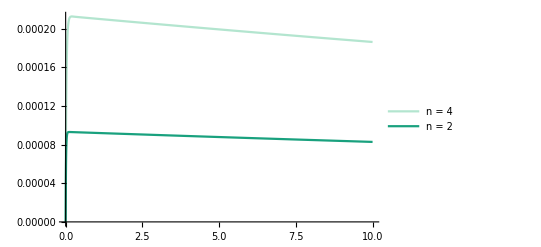

```mathematica
tmax=10;
Show[Trap4Energystored[4,1,100,42.5315,153.439],Trap4Energystored[2,1,100,42.5315,153.439]]
```

Trap population as a function of time:

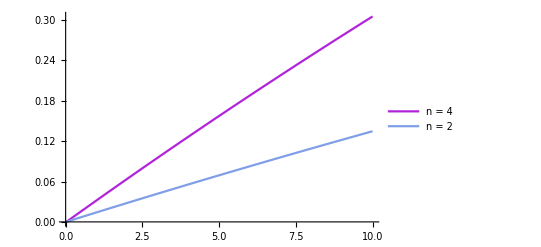

```mathematica
tmax=10;
Show[Trap4popPlot[4,1,100,42.5315,153.439],Trap4popPlot[2,1,100,42.5315,153.439]]
```

So here we see approx double gradient. So at large t we find trap charges twice as quick. But is that just because our trap atom is connected to double the amount of atoms so should be extracting twice the amount of excitons ?

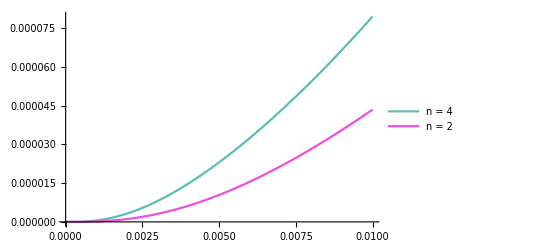

```mathematica
tmax=1/100;
Show[Trap4popPlot[4,1,100,42.5315,153.439],Trap4popPlot[2,1,100,42.5315,153.439]]
```

Pretty much just double, not really seeing an enhancement.

### Comparing 4 atoms to 2 atoms (using J+J- to measure excitations):

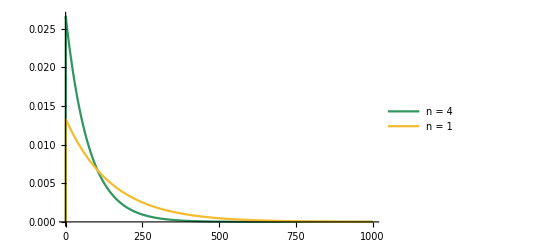

```mathematica
tmax=1000;
Show[Trap4popratePlot2[4,1,100,100,100],Trap4popratePlot2m4[1,1,100,100,100]]
```

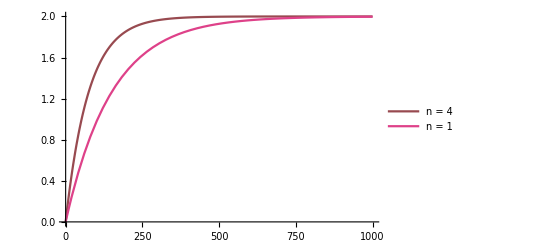

```mathematica
tmax=1000;
Show[Trap4popPlot2[4,1,100,100,100],Trap4popPlot2m4[1,1,100,100,100]]
```

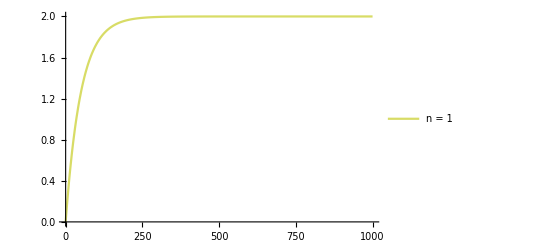

```mathematica
Trap4popPlot2m4[1,1,100,0,100]
```

```mathematica
tmax=1000;
Show[Trap4popratePlot2[4,1,100,1,100],Trap4popratePlot2[4,1,100,10,100],Trap4popratePlot2[4,1,100,100,100],Trap4popratePlot2[4,1,100,1000,100]]
```

Shows decreasing dephasing will just keep increasing trap population (And should see on same graph that charging rate increases also)
Try smaller trap rates to see if here dephasing gives advantage:

```mathematica
tmax=1000;
Show[Trap4popratePlot2[4,1,100,100,0.00001],Trap4popratePlot2[4,1,100,0,0.00001]]
```

Change trap rate and see if we have same trend as before:

```mathematica
tmax=1000;Show[Trap4popratePlot2[4,1,100,0,1],Trap4popratePlot2[4,1,100,0,100],Trap4popratePlot2[4,1,100,0,10000]]
```

Compare to individual atom:

```mathematica
tmax=1000;
Show[Trap4popratePlot2[4,1,100,0,100],Trap4popratePlot2[1,1,100,0,100]]
```

Compare traps ? or could just compare with discussion.

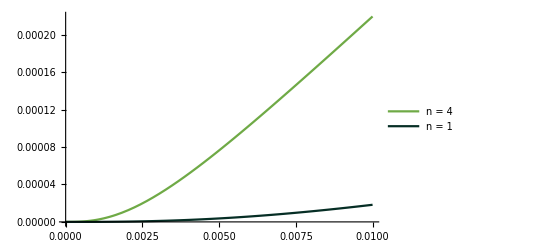

```mathematica
tmax=1/100;
Show[Trap4popPlot2[4,1,100,42.5315,153.439],Trap4popPlot2[1,1,100,42.5315,153.439]]
```

Again this shows larger trap population and more enhancement for n=4 atoms than for using σ+σ- to measure excitations.

Below we have the graph for n-traps and comparing to the collective trap above. It does seem to give larger charging power and a larger difference in the n=2 and n=4 atoms. So, shows more superextensive properties (maybe it doesnt as more traps means more extraction). However, It does involve 4 traps compared to the 1 trap in the collective case and obviously this will take up more space so isn’t necessarily more effective.

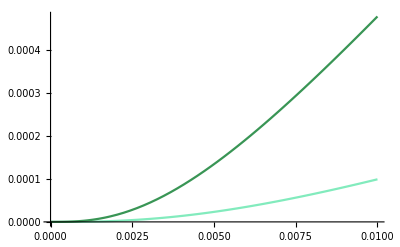

### Contour Plot:

```mathematica
Trap4pop[2,1,100,1,1000]
```

{0.000355201}

```mathematica
Trap4pop[2,1,100,0,1000]
```

{0.000326015}

```mathematica
Trap4pop[2,1,100,1,10]
```

{0.000301393}

```mathematica
Trap4pop[2,1,100,0,10]
```

{0.000285128}

```mathematica
Trap4pop[4,1,100,1,1000]
```

{0.000374956}

```mathematica
Trap4pop[2,1,100,0,1000]
```

{0.000326015}

So we see reduction in trap pop as we reduce dephasing if we measure exitations using pauli matrices but when using J+J- we do not see this ?????

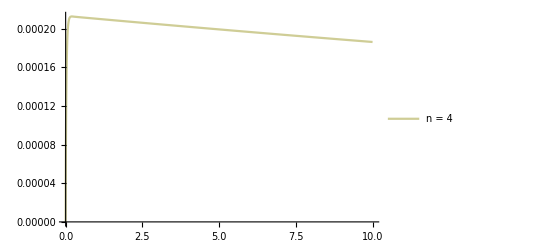

```mathematica
Trap4Energystored[4,1,100,42.5315,153.439]
```

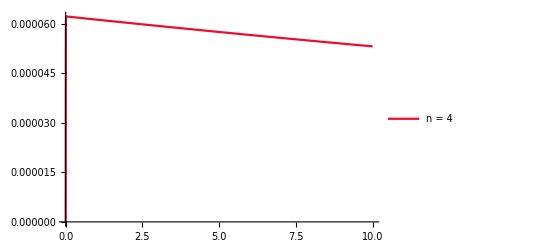

```mathematica
Trap4Energystored[4,1,100,0,153.439]
```

More energy stored but we dont get an advantage from collective with dephasing because this ruins the coherences so will reduce population. we also find it is optimum if dephasing is zero, because for collective, we want to remain on the dicke ladder, dark states dont help (look at brendons notes on collective, see the matrix element comes as zero) but collective trap is hard to do, single trap easier and here we do see dephasing work.

```mathematica
tmax=1/100;
Timing[Trap4pop2[4,1,100,30,150]]
```

$Aborted

So if i have a dephasing value and then increase trap rate, i will find a max. But if i fix trap and decrease dephasing, i will find it continues to increase???

```mathematica
tmax=1/100;
Trap4pop2[2,1,100,.1,150]
```

{0.0000890854}

```mathematica
tmax=1/100;
Trap4pop2[2,1,100,0,150]
```

{0.0000891454}

```mathematica
0.28523338030769857
```

```mathematica
0.00023213592763475643
```

```mathematica
Timing[trappop3[42.5315,153.439]]
```

{13.6406,{0.000219384}}

```mathematica
{Trap4pop2[4,1,100,30,153.439][[1]],Trap4pop2[4,1,100,40,153.439][[1]],Trap4pop2[4,1,100,50,153.439][[1]]}
```

{0.00322773,0.00311546,0.00301301}

Maybe if optical decay was very large we would find advantages of the dephasing storing energy???

```mathematica
Trap4pop2[4,1,1000,1,100][[1]]
```

0.000131095

```mathematica
Trap4pop2[4,1,1000,0,100][[1]]
```

0.000131299

```mathematica
f[x_,y_]:=Trap4pop2[4,1,100,x,y][[1]]
```

```mathematica
f2[x_]:=Trap4pop2[4,1,100,x,150][[1]]
```

```mathematica
Trap4pop2[4,1,100,10,153.439][[1]]
```

$Aborted

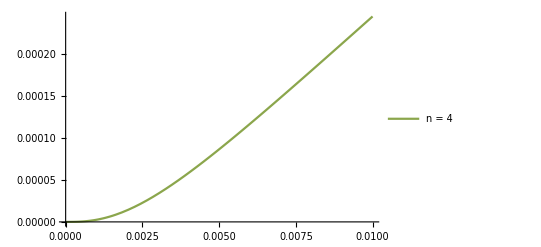

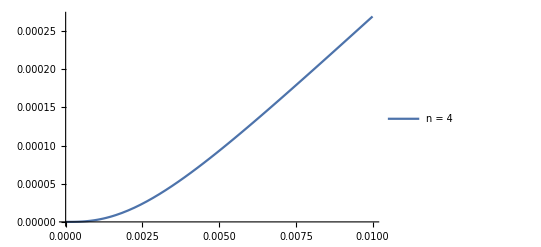

```mathematica
tmax=1/100;
Trap4popPlot2[4,1,100,20,180]
Trap4popPlot2[4,1,100,0.1,180]
```

```mathematica
f2[10]
```

Thread::tdlen: Objects of unequal length in 1/2 {10,20} {{0,0,0,0,0,0,0,0,4 ρ_(1,9)[t],4 ρ_(1,10)[t],«70»},{0,0,0,0,0,0,0,0,4 ρ_(2,9)[t],4 ρ_(2,10)[t],«70»},{0,0,0,0,0,0,0,0,4 ρ_(3,9)[t],4 ρ_(3,10)[t],«70»},{0,0,0,0,0,0,0,0,4 ρ_(4,9)[t],4 ρ_(4,10)[t],«70»},«4»,{4 ρ_(9,1)[t],4 ρ_(9,2)[t],4 ρ_(9,3)[t],4 ρ_(9,4)[t],4 ρ_(9,5)[t],4 ρ_(9,6)[t],4 ρ_(9,7)[t],4 ρ_(9,8)[t],0,0,«70»},{4 ρ_(10,1)[t],4 ρ_(10,2)[t],4 ρ_(10,3)[t],4 ρ_(10,4)[t],4 ρ_(10,5)[t],4 ρ_(10,6)[t],4 ρ_(10,7)[t],4 ρ_(10,8)[t],0,0,«70»},«70»} cannot be combined.

Thread::tdlen: Objects of unequal length in 1/2 {10,20} {{0,0,0,0,4 ρ_(1,5)[t],4 ρ_(1,6)[t],4 ρ_(1,7)[t],4 ρ_(1,8)[t],0,0,«70»},{0,0,0,0,4 ρ_(2,5)[t],4 ρ_(2,6)[t],4 ρ_(2,7)[t],4 ρ_(2,8)[t],0,0,«70»},{0,0,0,0,4 ρ_(3,5)[t],4 ρ_(3,6)[t],4 ρ_(3,7)[t],4 ρ_(3,8)[t],0,0,«70»},{0,0,0,0,4 ρ_(4,5)[t],4 ρ_(4,6)[t],4 ρ_(4,7)[t],4 ρ_(4,8)[t],0,0,«70»},«4»,{0,0,0,0,4 ρ_(9,5)[t],4 ρ_(9,6)[t],4 ρ_(9,7)[t],4 ρ_(9,8)[t],0,0,«70»},{0,0,0,0,4 ρ_(10,5)[t],4 ρ_(10,6)[t],4 ρ_(10,7)[t],4 ρ_(10,8)[t],0,0,«70»},«70»} cannot be combined.

Thread::tdlen: Objects of unequal length in 1/2 {10,20} «1» cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

NDSolve::ntdv: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

```mathematica
contourlist1=Table[{x,y,f[x,y]},{x,10,74,8},{y,140,160,4}]
```

NDSolve::ntdv: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

```mathematica
contourlist2=Table[{x,y,f[x,y]},{x,10,74,8},{y,164,204,4}]
```

$Aborted

```mathematica
contourlist2
```

{{{30,140,0.000229653},{30,144,0.000230523},{30,148,0.000231278},{30,152,0.000231927},{30,156,0.000232476},{30,160,0.000232931},{30,164,0.000233299},{30,168,0.000233584},{30,172,0.000233793},{30,176,0.000233929},{30,180,0.000233998}},{{34,140,0.000225307},{34,144,0.000226206},{34,148,0.000226994},{34,152,0.000227677},{34,156,0.00022826},{34,160,0.000228752},{34,164,0.000229156},{34,168,0.000229479},{34,172,0.000229726},{34,176,0.000229901},{34,180,0.000230008}},{{38,140,0.000221127},{38,144,0.000222056},{38,148,0.000222874},{38,152,0.000223587},{38,156,0.000224204},{38,160,0.000224728},{38,164,0.000225167},{38,168,0.000225526},{38,172,0.000225808},{38,176,0.00022602},{38,180,0.000226164}},{{42,140,0.000217107},{42,144,0.000218062},{42,148,0.000218908},{42,152,0.000219651},{42,156,0.000220298},{42,160,0.000220854},{42,164,0.000221325},{42,168,0.000221716},{42,172,0.000222032},{42,176,0.000222278},{42,180,0.000222458}},{{46,140,0.000213238},{46,144,0.000214217},{46,148,0.000215089},{46,152,0.000215859},{46,156,0.000216534},{46,160,0.00021712},{46,164,0.000217621},{46,168,0.000218043},{46,172,0.000218391},{46,176,0.000218669},{46,180,0.000218881}},{{50,140,0.000209511},{50,144,0.000210513},{50,148,0.000211409},{50,152,0.000212204},{50,156,0.000212906},{50,160,0.000213519},{50,164,0.000214049},{50,168,0.0002145},{50,172,0.000214878},{50,176,0.000215186},{50,180,0.000215429}},{{54,140,0.000205919},{54,144,0.000206942},{54,148,0.00020786},{54,152,0.00020868},{54,156,0.000209406},{54,160,0.000210045},{54,164,0.000210601},{54,168,0.00021108},{54,172,0.000211486},{54,176,0.000211822},{54,180,0.000212095}},{{58,140,0.000202456},{58,144,0.000203499},{58,148,0.000204437},{58,152,0.000205278},{58,156,0.000206028},{58,160,0.000206691},{58,164,0.000207272},{58,168,0.000207776},{58,172,0.000208208},{58,176,0.000208573},{58,180,0.000208874}},{{62,140,0.000199115},{62,144,0.000200175},{62,148,0.000201133},{62,152,0.000201994},{62,156,0.000202765},{62,160,0.000203451},{62,164,0.000204055},{62,168,0.000204584},{62,172,0.000205041},{62,176,0.000205432},{62,180,0.000205759}},{{66,140,0.000195889},{66,144,0.000196965},{66,148,0.000197941},{66,152,0.000198822},{66,156,0.000199613},{66,160,0.000200319},{66,164,0.000200946},{66,168,0.000201498},{66,172,0.00020198},{66,176,0.000202394},{66,180,0.000202746}},{{70,140,0.000192772},{70,144,0.000193864},{70,148,0.000194857},{70,152,0.000195755},{70,156,0.000196565},{70,160,0.000197291},{70,164,0.000197939},{70,168,0.000198513},{70,172,0.000199016},{70,176,0.000199454},{70,180,0.000199829}}}

```mathematica
f[30,200]
```

0.000233467

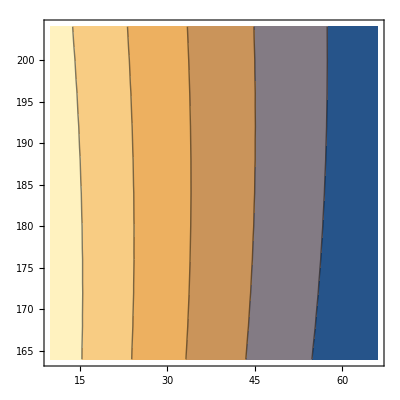

```mathematica
ListContourPlot[Join[contourlist2[[1]],contourlist2[[2]],contourlist2[[3]],contourlist2[[4]],contourlist2[[5]],contourlist2[[6]],contourlist2[[7]],contourlist2[[8]]]]
```

```mathematica
contourlist=Table[{a,b,Trap4pop2[4,1,100,a,153.439][[1]]},{a,30,50,10}]
```

$Aborted

## Two-level atom coupled collectively to all atoms. (Trap 5)

H_T=γt(J_+ (σ_-)^T+J_- (σ_+)^T)+ω_trap (σ_+)^T(σ_-)^T    (First part is coupling and will go both ways, second part is energy associated with trap. I will then add a lindblad dissipator ((σ_-)^T) with a very high rate so before exciton has the chance to go back into out battery system, the exciton will be removed. Therefore, we can still calculate the trap population the same as before with γt * J+J-. Trap at resonance (ω_trap = ω_a=ω_c).

### The Code

```mathematica
Trap5pop[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];
Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n+1].alown[n+1]},Table[ID,n+1]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+2],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}],ID];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+2],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}],ID];
Jplus=KroneckerProduct[IdentityMatrix[n+2],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}],ID];
Hn3rd=ωc*1(KroneckerProduct[alown[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}],ID]+KroneckerProduct[adagn[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}],ID]);
sigplust=KroneckerProduct[IdentityMatrix[n+2],FoldKP[Table[ID,n]],sigmaplusR];
sigminust=KroneckerProduct[IdentityMatrix[n+2],FoldKP[Table[ID,n]],sigmaminusR];
rhonL[t_]:=rho[Range[(n+2)*2^(n+1)],t];
initn=DiagonalMatrix[Join[Table[0,(n+2)*(2^(n+1))-1],{1}]];
L2=Expand[100(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])];
Htrap=γt(Jplus.sigplust+Jminus.sigminust)+ωt(sigplust.sigminust);
Hn=Hn1st+Hn2nd+Hn3rd+Htrap;
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni2[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminust,γto]];(*Should i include dephasing for trap atom???*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->Solve}];
trappop=NIntegrate[γt*Tr[rhonL[t].(Jplus.Jminus)]/.soln,{t,0,tmax}]);

γto=1000;
ωt=ωa;
L1ni2[n_,j_]:=KroneckerProduct[IdentityMatrix[n+2],FoldKP[Join[Table[ID,j-1],{L1},Table[ID,n-j]]],ID];
Trap5popPlot[n_,γd_,γt_]:=(
ID=IdentityMatrix[2];
Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n+1].alown[n+1]},Table[ID,n+1]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+2],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}],ID];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+2],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}],ID];
Jplus=KroneckerProduct[IdentityMatrix[n+2],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}],ID];
Hn3rd=ωc*1(KroneckerProduct[alown[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}],ID]+KroneckerProduct[adagn[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}],ID]);
sigplust=KroneckerProduct[IdentityMatrix[n+2],FoldKP[Table[ID,n]],sigmaplusR];
sigminust=KroneckerProduct[IdentityMatrix[n+2],FoldKP[Table[ID,n]],sigmaminusR];
rhonL[t_]:=rho[Range[(n+2)*2^(n+1)],t];
L2=100(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]]);
Htrap=γt(Jplus.sigplust+Jminus.sigminust)+ωt(sigplust.sigminust);
Hn=Hn1st+Hn2nd+Hn3rd+Htrap;
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni2[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminust,γto]];(*Should i include dephasing for trap atom???*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initLHSn=Flatten[rhonL[0]];
initn=DiagonalMatrix[Join[Table[0,(n+2)*(2^(n+1))-1],{1}]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->Solve}];
Plot[NIntegrate[γt*(Tr[rhonL[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}])
```

```mathematica
γto=1000;
ωt=ωa;
L1ni2[n_,j_]:=KroneckerProduct[IdentityMatrix[n+2],FoldKP[Join[Table[ID,j-1],{L1},Table[ID,n-j]]],ID];
L3[j_]:=L1ni2[4,j];
ID=IdentityMatrix[2];
Hn2ndlist=Join[Table[ID,4-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[4+1].alown[4+1]},Table[ID,4+1]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[4+2],Sum[FoldKP[n2ndperms[[i]]],{i,1,4}],ID];
n3rdplus=Join[Table[ID,4-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,4-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[4+2],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,4}],ID];
Jplus=KroneckerProduct[IdentityMatrix[4+2],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,4}],ID];
Hn3rd=ωc*1(KroneckerProduct[alown[4+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,4}],ID]+KroneckerProduct[adagn[4+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,4}],ID]);
sigplust=KroneckerProduct[IdentityMatrix[4+2],FoldKP[Table[ID,4]],sigmaplusR];
sigminust=KroneckerProduct[IdentityMatrix[4+2],FoldKP[Table[ID,4]],sigmaminusR];
rhonL[t_]:=rho[Range[(4+2)*2^(4+1)],t];
initn=DiagonalMatrix[Join[Table[0,(4+2)*(2^(4+1))-1],{1}]];
L2=Expand[100(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])];
Trap5Energystored[γd_,γt_]:=(
Htrap=γt(Jplus.sigplust+Jminus.sigminust)+ωt(sigplust.sigminust);
Hn=Hn1st+Hn2nd+Hn3rd+Htrap;
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni2[4,j],γd],{j,4}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminust,γto]];(*Should i include dephasing for trap atom???*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->Solve}];

Plot[Tr[rhonL[t].Hn2nd]/.soln,{t,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[4]}]);
```

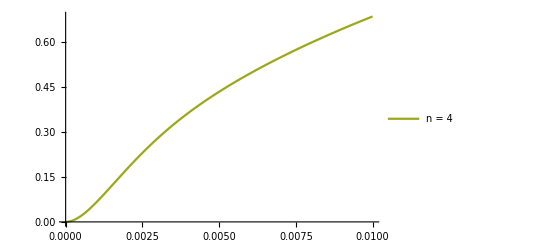

```mathematica
tmax=1/100;
Trap5Energystored[43,156]
```

```mathematica
L1ni2[n_,j_]:=KroneckerProduct[IdentityMatrix[n+2],FoldKP[Join[Table[ID,j-1],{L1},Table[ID,n-j]]],ID];
Trap5Energystored2[n_,γd_,γt_]:=(
ID=IdentityMatrix[2];
Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n+1].alown[n+1]},Table[ID,n+1]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+2],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}],ID];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+2],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}],ID];
Jplus=KroneckerProduct[IdentityMatrix[n+2],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}],ID];
Hn3rd=ωc*1(KroneckerProduct[alown[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}],ID]+KroneckerProduct[adagn[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}],ID]);
sigplust=KroneckerProduct[IdentityMatrix[n+2],FoldKP[Table[ID,n]],sigmaplusR];
sigminust=KroneckerProduct[IdentityMatrix[n+2],FoldKP[Table[ID,n]],sigmaminusR];
rhonL[t_]:=rho[Range[(n+2)*2^(n+1)],t];
initn=DiagonalMatrix[Join[Table[0,(n+2)*(2^(n+1))-1],{1}]];
L2=Expand[100(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])];
Htrap=γt(Jplus.sigplust+Jminus.sigminust)+ωt(sigplust.sigminust);
Hn=Hn1st+Hn2nd+Hn3rd+Htrap;
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni2[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminust,γto]];(*Should i include dephasing for trap atom???*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->Solve}];

Plot[Tr[rhonL[t].Hn2nd]/.soln,{t,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}]);
```

```mathematica
Trap5Energystored2[2,43,156]
```

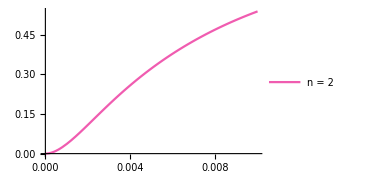
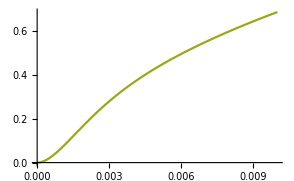

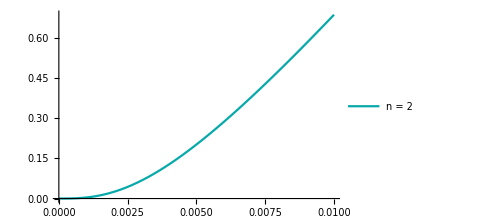
{42.9219,-Graphics-}

```mathematica
tmax=1/100;
Timing[Trap5popPlot[2,1,100,43,156]]
```

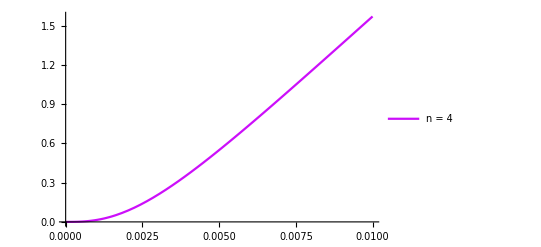
{5928.55,-Graphics-}

```mathematica
tmax=1/100;
Timing[Trap5popPlot[4,43,156]]
```

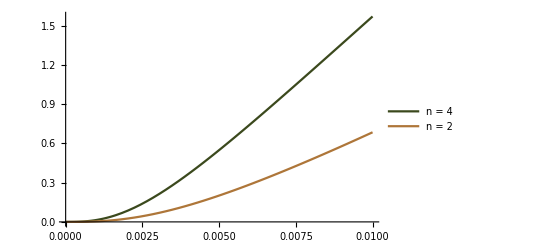

```mathematica
tmax=1/100;
Show[Trap5popPlot[4,43,156],Trap5popPlot[2,43,156]]
```

## I want to show superradiance in code, so initial state will be fully excited and photons lost to environment (so no cavity)

```mathematica
radiated[n_,γo_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn2nd=ωa Sum[FoldKP[n2ndperms[[i]]],{i,1,n}];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}];

Hn=Hn2nd;
rhonL[t_]:=rho[Range[2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*L2];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[{1},Table[0,(2^n)-1]]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];
firstpop=FoldKP[{{1,0},{0,0}},Table[ID,n-1]];
Plot[(Tr[rhonL[t].firstpop])/.soln,{t,0,tmax},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]}])
```

```mathematica
radiatedpower[n_,γo_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn2nd=ωa Sum[FoldKP[n2ndperms[[i]]],{i,1,n}];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}];

Hn=Hn2nd;
rhonL[t_]:=rho[Range[2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*L2];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[{1},Table[0,(2^n)-1]]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax}];
firstpop=FoldKP[{{1,0},{0,0}},Table[ID,n-1]];
Plot[-(Tr[rhonL'[t].firstpop])/.soln,{t,0,tmax/2},PlotRange->All,PlotStyle->RandomColor[],PlotLegends->{"n = "<>ToString[n]},AxesLabel->{"t","Rate"}])
```

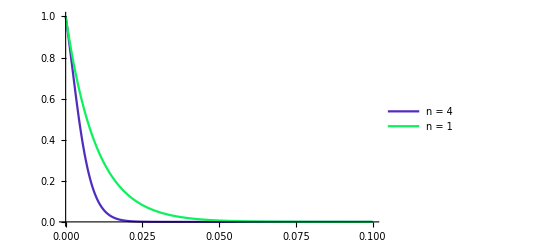

```mathematica
tmax=1/10;
Show[radiated[4,100],radiated[1,100]]
```

The above shows the occupancy of the excited state of a single atom in the 4 atom system and in an isolated atom.

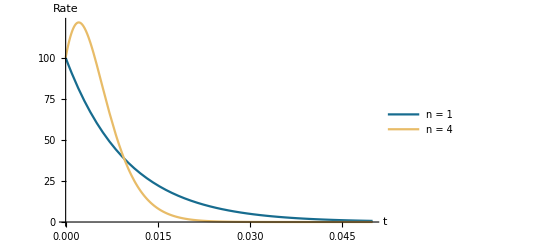

```mathematica
tmax=1/10;
Show[radiatedpower[1,100],radiatedpower[4,100]]
```

Above shows rate of radiation and we can see that the n=4 atoms have this superradiant burst (peak) then dies off quickly so at later times n=1 radiated at a larger rate but this is expected as they are radiating the same amount of photons in the end (1).

# Plots

I had to code on about 3 computers at once to create all the final plots on time so i am so sorry that the following is such a mess

# Trap 1:

### Energy stored

```mathematica
Trap1Energystoredb[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom, this takes an excitation from first atom and goes to the "trap"*)
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];

Plot[Tr[rhonL[t].Hn2nd]/.soln,{t,0,tmax},PlotRange->All,PlotStyle->Blue,PlotLegends->{"N = "<>ToString[n]},AxesLabel->{"t/s",""}])
```

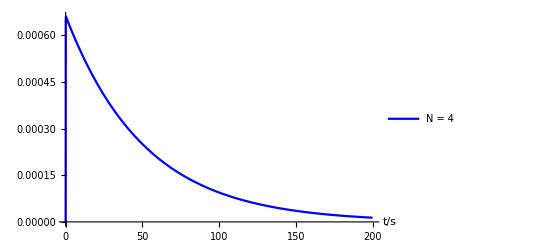

```mathematica
tmax=200;
Trap1Energystoredb[4,1,100,100,100]
```

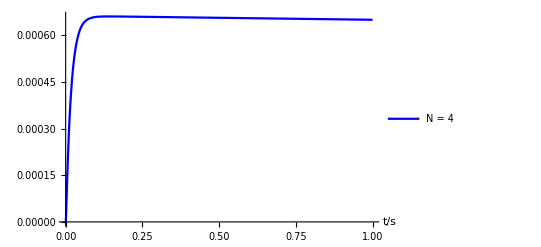

```mathematica
tmax=1;
Trap1Energystoredb[4,1,100,100,100]
```

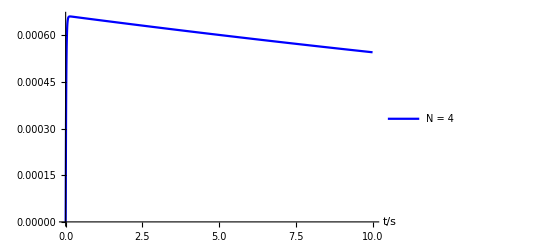

```mathematica
tmax=10;
Trap1Energystoredb[4,1,100,100,100]
```

## Trap population

### Red

```mathematica
Trap1popPlotr[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->Red,PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","Trap population"}])
```

```mathematica
Trap1popPlotrdashed[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->{Red,Dashing[Small]},PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","Trap population"}])
```

### Blue

```mathematica
Trap1popPlotb[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->Blue,PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","Trap population"}])
```

```mathematica
Trap1popPlotbdashed[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->{Blue,Dashing[Small]},PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","Trap population"}])
```

### Black

```mathematica
Trap1popPlotbl[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->Black,PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","Trap population"}])
```

```mathematica
Trap1popPlotbldashed[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->{Black,Dashing[Small]},PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","Trap population"}])
```

### Plots

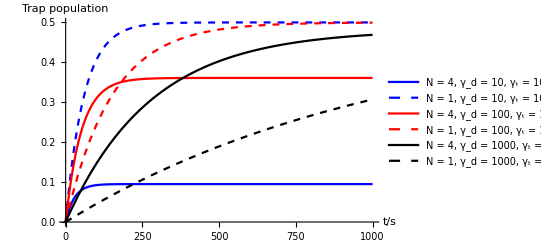

```mathematica
tmax=1000;
Show[Trap1popPlotb[4,1,100,10,100],Trap1popPlotbdashed[1,1,100,10,100],Trap1popPlotr[4,1,100,100,100],Trap1popPlotrdashed[1,1,100,100,100],Trap1popPlotbl[4,1,100,1000,100],Trap1popPlotbldashed[1,1,100,1000,100]]
```

Change “Trap population” to pT(t)

## Trap charging rate

### Red

```mathematica
Trap1popratePlotr[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL'[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->Red,PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","/"}])
```

```mathematica
Trap1popratePlotrdashed[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL'[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->{Red,Dashing[Small]},PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","/"}])
```

### Blue

```mathematica
Trap1popratePlotb[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL'[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->Blue,PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","/"}])
```

```mathematica
Trap1popratePlotbdashed[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL'[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->{Blue,Dashing[Small]},PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","/"}])
```

### Black

```mathematica
Trap1popratePlotbl[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL'[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->Black,PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","/"}])
```

```mathematica
Trap1popratePlotbldashed[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL'[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->{Black,Dashing[Small]},PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","/"}])
```

### Plots

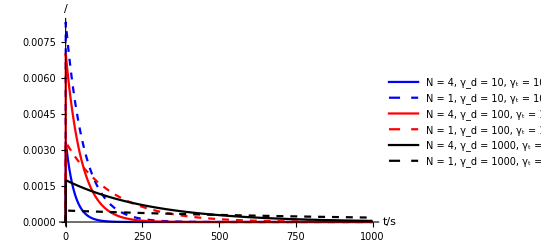

```mathematica
tmax=1000;
Show[Trap1popratePlotb[4,1,100,10,100],Trap1popratePlotbdashed[1,1,100,10,100],Trap1popratePlotr[4,1,100,100,100],Trap1popratePlotrdashed[1,1,100,100,100],Trap1popratePlotbl[4,1,100,1000,100],Trap1popratePlotbldashed[1,1,100,1000,100]]
```

TRY FOR A DIFFERENT OPTICAL DECAY, DOES N=1 STILL REACH 0.5 (HALF-FILLED) IF IT DOES THEN SHIT, HOW DO I EXPLAIN THAT

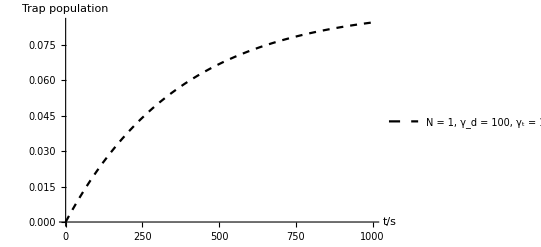

```mathematica
Trap1popPlotbldashed[1,1,1000,100,100]
```

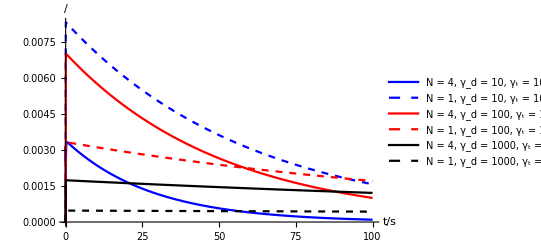

```mathematica
tmax=100;
Show[Trap1popratePlotb[4,1,100,10,100],Trap1popratePlotbdashed[1,1,100,10,100],Trap1popratePlotr[4,1,100,100,100],Trap1popratePlotrdashed[1,1,100,100,100],Trap1popratePlotbl[4,1,100,1000,100],Trap1popratePlotbldashed[1,1,100,1000,100]]
```

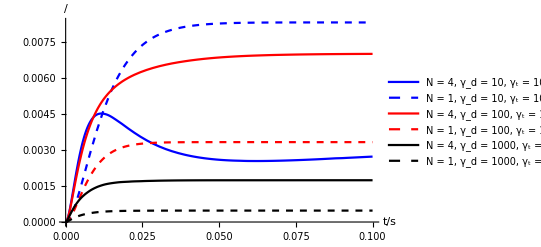

```mathematica
tmax=0.1;
Show[Trap1popratePlotb[4,1,100,10,100],Trap1popratePlotbdashed[1,1,100,10,100],Trap1popratePlotr[4,1,100,100,100],Trap1popratePlotrdashed[1,1,100,100,100],Trap1popratePlotbl[4,1,100,1000,100],Trap1popratePlotbldashed[1,1,100,1000,100]]
```

Changing gamma t instead (trap population)

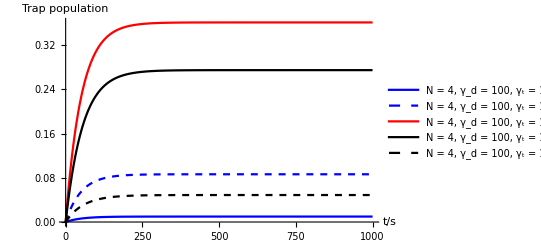

```mathematica
tmax=1000;
Show[Trap1popPlotb[4,1,100,100,1],Trap1popPlotbdashed[4,1,100,100,10],Trap1popPlotr[4,1,100,100,100],Trap1popPlotbl[4,1,100,100,1000],Trap1popPlotbldashed[4,1,100,100,10000]]
```

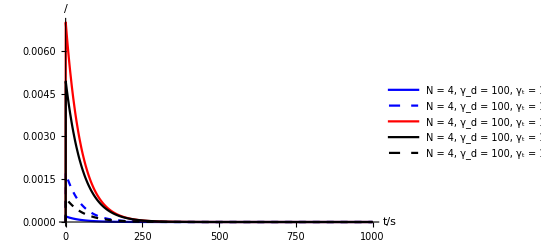

```mathematica
tmax=1000;
Show[Trap1popratePlotb[4,1,100,100,1],Trap1popratePlotbdashed[4,1,100,100,10],Trap1popratePlotr[4,1,100,100,100],Trap1popratePlotbl[4,1,100,100,1000],Trap1popratePlotbldashed[4,1,100,100,10000]]
```

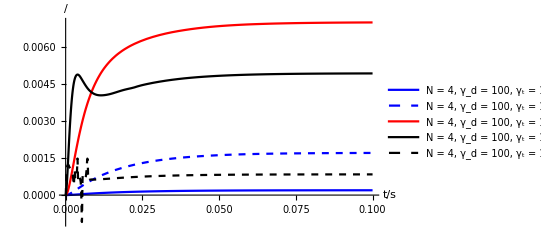

```mathematica
tmax=0.1;
Show[Trap1popratePlotb[4,1,100,100,1],Trap1popratePlotbdashed[4,1,100,100,10],Trap1popratePlotr[4,1,100,100,100],Trap1popratePlotbl[4,1,100,100,1000],Trap1popratePlotbldashed[4,1,100,100,10000]]
```

To plot long time trap population as a function of gamma t:

```mathematica
Trap1poptmax[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax}];
NIntegrate[γt*(Tr[rhonL[t].firstpop])/.soln,{t,0,tmax}])
```

```mathematica
tmax=1000;
zenolist=Table[{i,Trap1poptmax[4,1,100,100,i][[1]]},{i,1,10000,100}](*might have to do log plot*)
```

{{1,0.00984612},{101,0.361985},{201,0.4042},{301,0.398444},{401,0.380853},{501,0.360629},{601,0.340671},{701,0.321935},{801,0.304685},{901,0.28892},{1001,0.274544},{1101,0.261428},{1201,0.249441},{1301,0.238459},{1401,0.228375},{1501,0.219086},{1601,0.210509},{1701,0.202565},{1801,0.195193},{1901,0.188331},{2001,0.181931},{2101,0.175947},{2201,0.170343},{2301,0.165083},{2401,0.160134},{2501,0.155473},{2601,0.151075},{2701,0.146918},{2801,0.142983},{2901,0.139253},{3001,0.135712},{3101,0.132338},{3201,0.129144},{3301,0.126095},{3401,0.123182},{3501,0.120403},{3601,0.117746},{3701,0.115208},{3801,0.112769},{3901,0.110433},{4001,0.108192},{4101,0.106043},{4201,0.103974},{4301,0.101988},{4401,0.100074},{4501,0.0982327},{4601,0.0964559},{4701,0.0947433},{4801,0.0930901},{4901,0.0914928},{5001,0.0899493},{5101,0.0884574},{5201,0.0870141},{5301,0.0856159},{5401,0.0842613},{5501,0.0829523},{5601,0.0816837},{5701,0.0804504},{5801,0.0792551},{5901,0.0780953},{6001,0.0769683},{6101,0.0758717},{6201,0.074809},{6301,0.0737744},{6401,0.0727691},{6501,0.0717894},{6601,0.0708362},{6701,0.0699064},{6801,0.0690016},{6901,0.0681239},{7001,0.0672614},{7101,0.0664264},{7201,0.0656075},{7301,0.0648105},{7401,0.0640326},{7501,0.0632729},{7601,0.0625315},{7701,0.0618059},{7801,0.0610964},{7901,0.0604071},{8001,0.0597291},{8101,0.059069},{8201,0.0584212},{8301,0.0577871},{8401,0.0571703},{8501,0.0565636},{8601,0.0559707},{8701,0.0553895},{8801,0.0548199},{8901,0.0542625},{9001,0.0537154},{9101,0.0531804},{9201,0.0526543},{9301,0.052139},{9401,0.051633},{9501,0.0511384},{9601,0.0506543},{9701,0.0501778},{9801,0.0497102},{9901,0.0492512}}

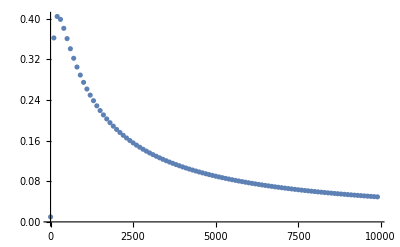

```mathematica
ListPlot[zenolist]
```

```mathematica
tmax=1000;
zenolist2=Table[{i,Trap1poptmax[4,1,100,100,i][[1]]},{i,1,1000,10}]
```

{{1,0.00984612},{11,0.0936633},{21,0.157029},{31,0.206057},{41,0.24467},{51,0.275501},{61,0.300383},{71,0.320621},{81,0.337178},{91,0.350786},{101,0.361985},{111,0.371207},{121,0.378789},{131,0.385001},{141,0.390059},{151,0.394141},{161,0.397391},{171,0.39993},{181,0.401856},{191,0.403247},{201,0.4042},{211,0.404748},{221,0.404973},{231,0.40486},{241,0.404504},{251,0.403919},{261,0.403133},{271,0.402173},{281,0.401059},{291,0.39981},{301,0.398444},{311,0.396976},{321,0.395417},{331,0.39378},{341,0.392074},{351,0.39031},{361,0.388495},{371,0.386635},{381,0.384738},{391,0.382809},{401,0.380853},{411,0.378876},{421,0.37688},{431,0.374869},{441,0.372848},{451,0.370818},{461,0.368783},{471,0.366744},{481,0.364704},{491,0.362665},{501,0.360629},{511,0.358596},{521,0.356568},{531,0.354549},{541,0.35253},{551,0.350532},{561,0.348538},{571,0.346554},{581,0.344581},{591,0.34262},{601,0.340671},{611,0.338735},{621,0.336812},{631,0.334902},{641,0.333006},{651,0.331125},{661,0.329258},{671,0.327405},{681,0.325567},{691,0.323744},{701,0.321935},{711,0.320142},{721,0.318364},{731,0.316601},{741,0.314854},{751,0.313121},{761,0.311403},{771,0.309701},{781,0.308014},{791,0.306342},{801,0.304685},{811,0.303043},{821,0.301413},{831,0.299803},{841,0.298205},{851,0.296622},{861,0.295053},{871,0.293498},{881,0.291958},{891,0.290432},{901,0.28892},{911,0.287424},{921,0.285938},{931,0.284467},{941,0.283006},{951,0.281566},{961,0.280136},{971,0.278719},{981,0.277315},{991,0.275922}}

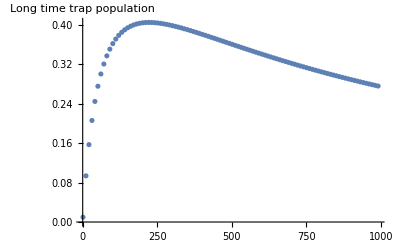

```mathematica
Show[ListPlot[zenolist2],AxesLabel->{"","Long time trap population"}]
```

## PLOTS

## Blue

```mathematica
Trap4popPlot2b[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->Blue,PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","Trap population"}])
```

```mathematica
Trap4popPlot2m4b[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[4*γt*(Tr[rhonL[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->{Blue,Dashing[Small]},PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","Trap population"}])
```

```mathematica
Trap4popratePlot2b[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL'[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->{Blue},PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","Charging rate/s^-1"}])
```

```mathematica
Trap4popratePlot2m4b[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[4*γt*(Tr[rhonL'[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->{Blue,Dashing[Small]},PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t","Charging rate/s^-1"}])
```

## Red

```mathematica
Trap4popPlot2r[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->Red,PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","Trap population"}])
```

```mathematica
Trap4popPlot2m4r[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[4*γt*(Tr[rhonL[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->{Red,Dashing[Small]},PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","Trap population"}])
```

```mathematica
Trap4popratePlot2r[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL'[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->{Red},PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","Charging rate/s^-1"}])
```

```mathematica
Trap4popratePlot2m4r[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[4*γt*(Tr[rhonL'[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->{Red,Dashing[Small]},PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t","Charging rate/s^-1"}])
```

## Black

```mathematica
Trap4popPlot2bl[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->Black,PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","Trap population"}])
```

```mathematica
Trap4popPlot2m4bl[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[4*γt*(Tr[rhonL[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->{Black,Dashing[Small]},PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","Trap population"}])
```

```mathematica
Trap4popratePlot2bl[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL'[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->{Black},PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t/s","Charging rate/s^-1"}])
```

```mathematica
Trap4popratePlot2m4bl[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[4*γt*(Tr[rhonL'[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->{Black,Dashing[Small]},PlotLegends->{"N = "<>ToString[n]<>", γ_d = "<>ToString[γd]<>", γ_t = "<>ToString[γt]},AxesLabel->{"t","Charging rate/s^-1"}])
```

## Plotting

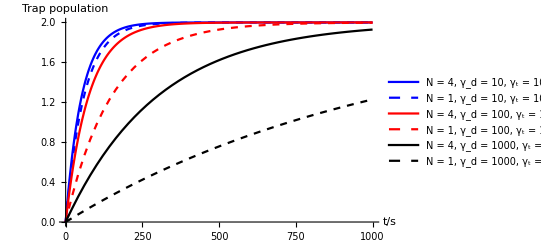

```mathematica
tmax=1000;
Show[Trap4popPlot2b[4,1,100,10,100],Trap4popPlot2m4b[1,1,100,10,100],Trap4popPlot2r[4,1,100,100,100],Trap4popPlot2m4r[1,1,100,100,100],Trap4popPlot2bl[4,1,100,1000,100],Trap4popPlot2m4bl[1,1,100,1000,100]]
```

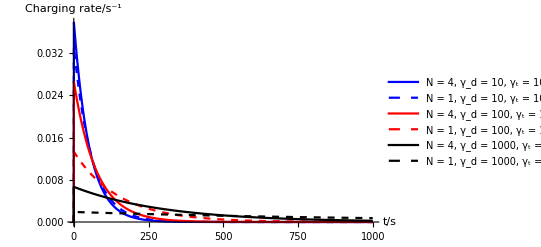

```mathematica
tmax=1000;
Show[Trap4popratePlot2b[4,1,100,10,100],Trap4popratePlot2m4b[1,1,100,10,100],Trap4popratePlot2r[4,1,100,100,100],Trap4popratePlot2m4r[1,1,100,100,100],Trap4popratePlot2bl[4,1,100,1000,100],Trap4popratePlot2m4bl[1,1,100,1000,100]]
```

## trap pop compare

```mathematica
Trap1popPlotbl2[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[4*γt*(Tr[rhonL[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->Black,PlotLegends->{"Trap 1"}])
```

```mathematica
Trap3popPlot2b2[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom*)
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
(*acts only on second atom - This is our "second trap"*)(*so we are just removing excitions again but from 2 atoms now*)
sigminusi[i_]:=KroneckerProduct[IdentityMatrix[n+1],FoldKP[Table[ID,i]],FoldKP[sigmaminusR,Table[ID,n-i-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
L3=Sum[L[rhonL[t],sigminusi[x],γt],{x,1,n-1}]+L[rhonL[t],sigminus1,γt];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L3];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->Blue,PlotLegends->{"Trap 2"},AxesLabel->{"t/s","Trap population"}])
```

```mathematica
Trap4popPlot2r2[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->Red,PlotLegends->{"Trap 3"},AxesLabel->{"t/s","Trap population"}])
```

```mathematica
T3plot1=Trap4popPlot2r2[4,1,100,100,100];
T2plot1=Trap3popPlot2b2[4,1,100,100,100];

T3plot2=Trap4popPlot2r2[4,1,100,10,100];
T2plot2=Trap3popPlot2b2[4,1,100,10,100];

T3plot3=Trap4popPlot2r2[4,1,100,1000,100];
T2plot3=Trap3popPlot2b2[4,1,100,1000,100];
```

Scale it!!!

```mathematica
T1plot1=Trap1popPlotbl2[4,1,100,100,100];
T1plot2=Trap1popPlotbl2[4,1,100,10,100];
T1plot3=Trap1popPlotbl2[4,1,100,1000,100];
```

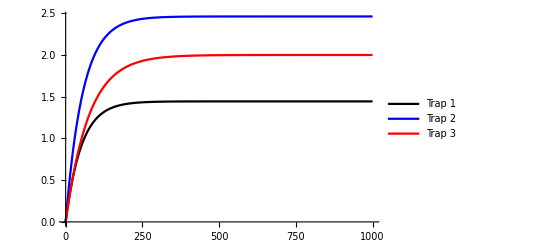

```mathematica
Show[T1plot1,T2plot1,T3plot1,AxesLabel->{"t/s","Trap population"}]
```

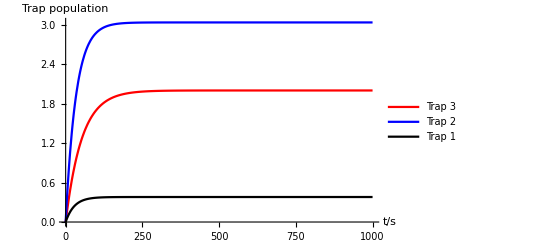

```mathematica
Show[T3plot2,
T2plot2,
T1plot2]
```

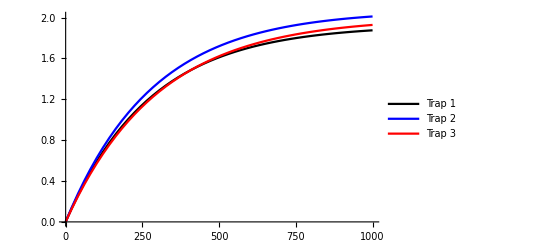

```mathematica
Show[T1plot3,T2plot3,T3plot3,AxesLabel->{"t/s","Trap population"}]
```

Want to see for very low dephasing also:

```mathematica
T3plot4=Trap4popPlot2r2[4,1,100,0,100];
T2plot4=Trap3popPlot2b2[4,1,100,0,100];
T1plot4=Trap1popPlotbl2[4,1,100,0,100];
```

Now same but for charging:

## Trap charging compare

```mathematica
Trap1popratePlotbl2[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[4*γt*(Tr[rhonL'[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->Black,PlotLegends->{"Trap 1"},AxesLabel->{"t","Charging rate/s^-1"}])
```

```mathematica
Trap3popratePlot2b2[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom*)
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
(*acts only on second atom - This is our "second trap"*)(*so we are just removing excitions again but from 2 atoms now*)
sigminusi[i_]:=KroneckerProduct[IdentityMatrix[n+1],FoldKP[Table[ID,i]],FoldKP[sigmaminusR,Table[ID,n-i-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
L3=Sum[L[rhonL[t],sigminusi[x],γt],{x,1,n-1}]+L[rhonL[t],sigminus1,γt];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L3];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL'[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->Blue,PlotLegends->{"Trap 2"},AxesLabel->{"t","Charging rate/s^-1"}])
```

```mathematica
Trap4popratePlot2r2[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],Jminus,γt]];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL'[t].(Jplus.Jminus)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->Red,PlotLegends->{"Trap 3"},AxesLabel->{"t","Charging rate/s^-1"}])
```

```mathematica
Trap1popratePlotdashed[n_,λ_,γo_,γd_,γt_]:=(
ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];(*so if the first atom has an electron in excited state it will return a value as remember the top left corresponds to excitate state*)
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];(*so if the second atom has an electron in excited state it will return a value*)
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];(*so if the third atom has an electron in excited state it will return a value and so on but the last two are just for comparisons, not important*)

Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L[rhonL[t],sigminus1,γt]];
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL'[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[4*γt*(Tr[rhonL'[t].firstpop])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->{Blue,Dashing[Small]},PlotLegends->{"Independent atoms"},AxesLabel->{"t","Charging rate/s^-1"}])
```

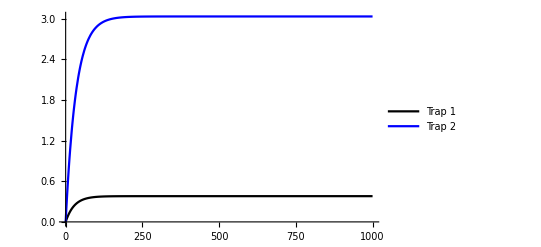

```mathematica
Show[Trap1popPlotbl2[4,1,100,10,100],Trap3popPlot2b2[4,1,100,10,100]]
```

### Plots

```mathematica
tmax=1000;
T1plotrate1=Trap1popratePlotbl2[4,1,100,10,100];
T3plotrate1=Trap4popratePlot2r2[4,1,100,10,100];
```

```mathematica
tmax=1000;
T0plotrate1=Trap1popratePlotdashed[1,1,100,10,100];
```

```mathematica
tmax=1000;
T1plotrate2=Trap1popratePlotbl2[4,1,100,100,100];
T3plotrate2=Trap4popratePlot2r2[4,1,100,100,100];
```

```mathematica
tmax=1000;
T0plotrate2=Trap1popratePlotdashed[1,1,100,100,100];
```

```mathematica
tmax=0.1;
T1plotrate11=Trap1popratePlotbl2[4,1,100,10,100];
T3plotrate11=Trap4popratePlot2r2[4,1,100,10,100];
```

```mathematica
tmax=0.1;
T0plotrate11=Trap1popratePlotdashed[1,1,100,10,100];
```

```mathematica
tmax=0.1;
T1plotrate22=Trap1popratePlotbl2[4,1,100,100,100];
T3plotrate22=Trap4popratePlot2r2[4,1,100,100,100];
```

```mathematica
tmax=0.1;
T0plotrate22=Trap1popratePlotdashed[1,1,100,100,100];
```

```mathematica
tmax=0.1;
T3plotrate44=Trap4popratePlot2r2[4,1,100,0,100];
```

```mathematica
tmax=0.1;
T0plotrate44=Trap1popratePlotdashed[1,1,100,0,100];
```

```mathematica
tmax=1000;
T0plotrate4=Trap1popratePlotdashed[1,1,100,0,100];
```

```mathematica
Show[T1plotrate44,T3plotrate44,T0plotrate44]
```

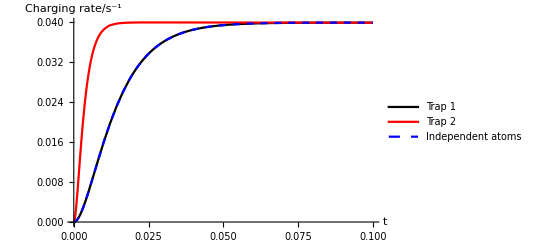

-Graphics-

```mathematica
Show[T1plotrate11,T3plotrate11,T0plotrate11]
```

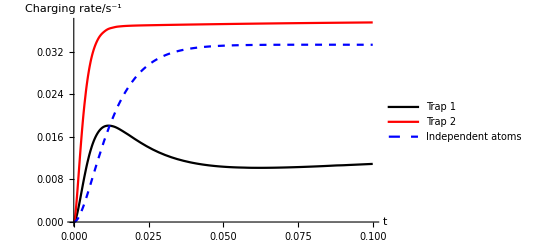

-Graphics-

```mathematica
Show[T1plotrate22,T3plotrate22,T0plotrate22]
```

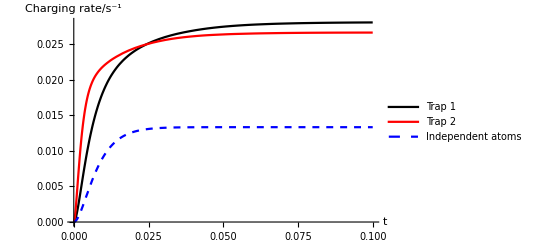

-Graphics-

```mathematica
Show[T1plotrate1,T3plotrate1,T0plotrate1]
```

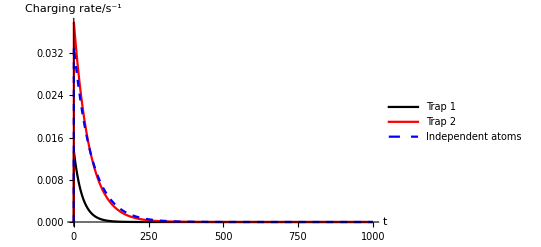

-Graphics-

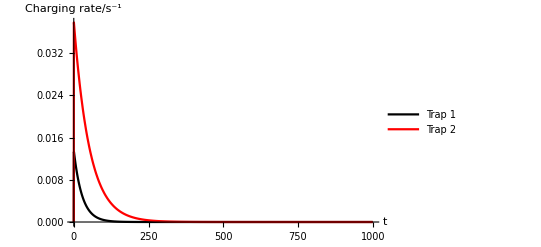

-Graphics-

```mathematica
Show[T1plotrate2,T3plotrate2,T0plotrate2]
```

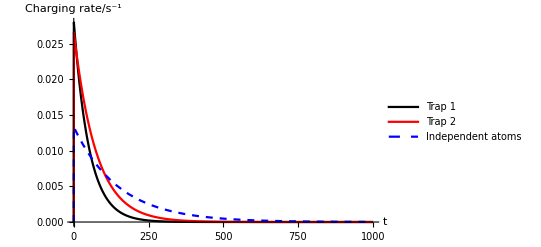

-Graphics-

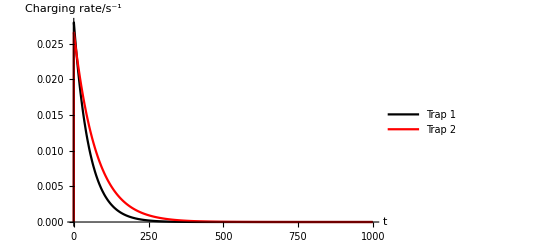

-Graphics-

```mathematica
Trap3popPlot1b[n_,λ_,γo_,γd_,γt_]:=(ID=IdentityMatrix[2];Hn2ndlist=Join[Table[ID,n-1],{sigmazR}];
n2ndperms=Permutations[Hn2ndlist];
Hn1st=ωc FoldKP[Join[{adagn[n].alown[n]},Table[ID,n]]];
Hn2nd=ωa KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n2ndperms[[i]]],{i,1,n}]];
n3rdplus=Join[Table[ID,n-1],{sigmaplusR}];
n3rdplusperm=Permutations[n3rdplus];
n3rdminus=Join[Table[ID,n-1],{sigmaminusR}];
n3rdminusperm=Permutations[n3rdminus];
Jminus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]];
Jplus=KroneckerProduct[IdentityMatrix[n+1],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]];
sigminus1=KroneckerProduct[IdentityMatrix[n+1],FoldKP[sigmaminusR,Table[ID,n-1]]];(*acts only on first atom*)
sigminus2=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[sigmaminusR,Table[ID,n-2]]];
(*acts only on second atom - This is our "second trap"*)(*so we are just removing excitions again but from 2 atoms now*)
sigminusi[i_]:=KroneckerProduct[IdentityMatrix[n+1],FoldKP[Table[ID,i]],FoldKP[sigmaminusR,Table[ID,n-i-1]]];
firstpop=KroneckerProduct[IdentityMatrix[n+1],FoldKP[{{1,0},{0,0}},Table[ID,n-1]]];
secpop=KroneckerProduct[IdentityMatrix[n+1],ID,FoldKP[{{1,0},{0,0}},Table[ID,n-2]]];
thirdpop=KroneckerProduct[IdentityMatrix[n+1],ID,ID,FoldKP[{{1,0},{0,0}},Table[ID,n-3]]];
fourthpop=KroneckerProduct[IdentityMatrix[4+1],ID,ID,ID,{{1,0},{0,0}}];
Hn3rd=ωc*λ(KroneckerProduct[alown[n],Sum[FoldKP[n3rdplusperm[[i]]],{i,1,n}]]+KroneckerProduct[adagn[n],Sum[FoldKP[n3rdminusperm[[i]]],{i,1,n}]]);
Hn=Hn1st+Hn2nd+Hn3rd;
rhonL[t_]:=rho[Range[(n+1)*2^n],t];
L2=Simplify[Expand[γo(Conjugate[Transpose[Jminus]].Jminus.rhonL[t]/2+rhonL[t].Conjugate[Transpose[Jminus]].Jminus/2-Jminus.rhonL[t].Conjugate[Transpose[Jminus]])]];
L3=Sum[L[rhonL[t],sigminusi[x],γt],{x,1,n-1}]+L[rhonL[t],sigminus1,γt];
RHSn=Flatten[Hn.rhonL[t]-rhonL[t].Hn-ⅈ*Sum[L[rhonL[t],L1ni[n,j],γd],{j,n}]-ⅈ*L2-ⅈ*L3];(*This extra lindblad term is our trap*)
LHSn=ⅈ*Flatten[D[rhonL[t],t]];
eqsn=Table[LHSn[[j]]==RHSn[[j]],{j,1,Length[LHSn]}];
initn=DiagonalMatrix[Join[Table[0,(n+1)*(2^n)-1],{1}]];
initLHSn=Flatten[rhonL[0]];
initRHSn=Flatten[initn];
initeqsn=Table[initLHSn[[k]]==initRHSn[[k]],{k,1,Length[initLHSn]}];
joineqsn=Join[eqsn,initeqsn];
soln=NDSolve[joineqsn,Flatten[rhonL[t]],{t,0,tmax},Method->{"EquationSimplification"->"Solve"}];
Plot[NIntegrate[γt*(Tr[rhonL[t].(firstpop)]+Tr[rhonL[t].(secpop)]+Tr[rhonL[t].(thirdpop)]+Tr[rhonL[t].(fourthpop)])/.soln,{t,0,tp}],{tp,0,tmax},PlotRange->All,PlotStyle->Blue,PlotLegends->{"Trap 2"},AxesLabel->{"t/s","Trap population"}])
```

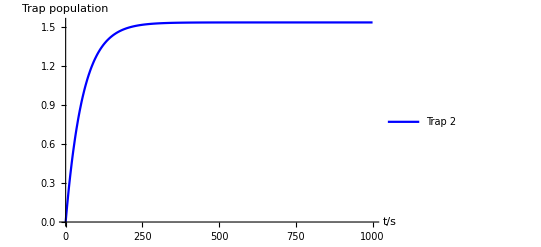

```mathematica
tmax=1000;
Trap3popPlot1b[4,1,100,100,100]
```